Before running anything in this notebook, MAR_dataruns0.nb must be run.

```mathematica
ptsize=8;
```

```mathematica
{0.5,0.6}
```

## Simulated B Matrix Generation

```mathematica
For[i=1,i≤1000,i++,
genb[i]=GenBNew[RandomInteger[{3,7}]];
]
```

```mathematica
For[i=1,i≤1000,i++,
genbL[i]=GenBNew[RandomInteger[{4,7}]];
]
```

```mathematica
For[i=1,i≤200,i++,
genbrange[i]=GenBNewrange[RandomInteger[{3,5}],0.5,0.6];
]
For[i=201,i≤400,i++,
genbrange[i]=GenBNewrange[RandomInteger[{3,5}],0.6,0.7];
]
For[i=401,i≤600,i++,
genbrange[i]=GenBNewrange[RandomInteger[{3,5}],0.7,0.8];
]
For[i=601,i≤800,i++,
genbrange[i]=GenBNewrange[RandomInteger[{3,5}],0.8,0.9];
]
For[i=801,i≤1000,i++,
genbrange[i]=GenBNewrange[RandomInteger[{3,5}],0.9,1];
]
```

## Function and List Initializations

### Here is a collection of functions that give a numerical property of a matrix:

```mathematica
(*Theoretical Measures of Stability*)
MaxEig[matrix_]:=-Log[Max[Abs[Eigenvalues[matrix]]]]

IntrinsicStochasticInvariability[bmatrix_]:=1/Norm[Inverse[IdentityMatrix[Dimensions[bmatrix][[1]]^2]-KroneckerProduct[bmatrix,bmatrix]],2]

Reactivity[matrix_]:=-Log[Sqrt[Max[Eigenvalues[Transpose[matrix].matrix]]]]

FrobeniusNorm[matrix_]:=Norm[matrix,"Frobenius"]

(* Mean Interaction Strengths *)
MeanInteractionStrength[bmatrix_]:=Total[Abs[bmatrix],2]/Dimensions[bmatrix][[1]]/Dimensions[bmatrix][[2]]

MeanInteractionStrengthExact[bmatrix_]:=Total[bmatrix,2]/Dimensions[bmatrix][[1]]/Dimensions[bmatrix][[2]]

MeanOffDiagonalInteractionStrength[bmatrix_]:=Total[Abs[UpperTriangularize[bmatrix,1]+LowerTriangularize[bmatrix,-1]],2]/(Dimensions[bmatrix][[1]]^2-Dimensions[bmatrix][[1]])

(* Specific Interaction Strengths *)
BottomUp[bmatrix_]:=Total[Abs[bmatrix[[1;;Length[bmatrix]-2,Length[bmatrix]-1;;Length[bmatrix]]]],2]/(2*(Length[bmatrix]-2))

BottomEd[bmatrix_]:=Total[Abs[bmatrix[[1;;Length[bmatrix]-2,Length[bmatrix]-1]]],2]/(Length[bmatrix]-2)
BottomIned[bmatrix_]:=Total[Abs[bmatrix[[1;;Length[bmatrix]-2,Length[bmatrix]]]],2]/(Length[bmatrix]-2)

TopDown[bmatrix_]:=Total[Abs[bmatrix[[Length[bmatrix]-1;;Length[bmatrix],1;;Length[bmatrix]-2]]],2]/(2*(Length[bmatrix]-2))

TopEd[bmatrix_]:=Total[Abs[bmatrix[[Length[bmatrix]-1,1;;Length[bmatrix]-2]]],2]/(Length[bmatrix]-2)
TopIned[bmatrix_]:=Total[Abs[bmatrix[[Length[bmatrix],1;;Length[bmatrix]-2]]],2]/(Length[bmatrix]-2)

MeanCompetition[bmatrix_]:=If[Length[bmatrix]==3,
0,
(Total[Abs[UpperTriangularize[bmatrix,1][[All,2;;Length[bmatrix]-2]]],2]+Total[Abs[LowerTriangularize[bmatrix,-1][[2;;Length[bmatrix]-2,All]]],2])/(Length[bmatrix]^2-5Length[bmatrix]+6)
]

(* Ratios of Specific Interaction Strengths *)
TopRatioEdIned[bmatrix_]:=TopEd[bmatrix]/TopIned[bmatrix]
BotRatioEdIned[bmatrix_]:=BottomEd[bmatrix]/BottomIned[bmatrix]

TopBottomRatio[bmatrix_]:=Total[Abs[bmatrix[[Length[bmatrix]-1;;Length[bmatrix],1;;Length[bmatrix]-2]]],2]/Total[Abs[bmatrix[[1;;Length[bmatrix]-2,Length[bmatrix]-1;;Length[bmatrix]]]],2]

BottomTopRatio[bmatrix_]:=Total[Abs[bmatrix[[1;;Length[bmatrix]-2,Length[bmatrix]-1;;Length[bmatrix]]]],2]/Total[Abs[bmatrix[[Length[bmatrix]-1;;Length[bmatrix],1;;Length[bmatrix]-2]]],2]
```

### Here are several bits of code that create lists of properties of the data that are not simple to obtain

```mathematica
(* This creates a list that tells if Daphnia is present in each treatment (2 for containing Daphnia, 1 for not) *)
containsDap={};
For[i=18,i≤32,i++,
size=Dimensions[bb[i]][[1]];
If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
containsDap=Join[containsDap,{2}],
containsDap=Join[containsDap,{1}]
];
]
```

#### Specific Elements

```mathematica
(* This creates a lot of lists containing the average interaction strengths of/on edible or inedible algae
Be is bottom up edible, Bi is bottom up inedible, Te is top down edible, Ti is top down inedible
These lists can be used to examine the effects related to one species (such as daplistBe)
 If the end of a list has avg in its name, it uses the averaged B matrices. Otherwise, the composite matrices are used. *)

(* Initialize lists *)
cerlistBe={}; cerlistBi={};
daplistBe={};daplistBi={};
scalistBe={};scalistBi={};
cerlistTe={};cerlistTi={};
daplistTe={};daplistTi={};
scalistTe={};scalistTi={};

cerlistBeavg={}; cerlistBiavg={};
daplistBeavg={};daplistBiavg={};
scalistBeavg={};scalistBiavg={};
cerlistTeavg={};cerlistTiavg={};
daplistTeavg={};daplistTiavg={};
scalistTeavg={};scalistTiavg={};

For[i=18,i≤32,i++, (* Loop over treatments *)
size=Dimensions[bb[i]][[1]];
If[MemberQ[rawdata[i][[1]],"Cer_ug"],(* Check if a species is present *)
For[j=1,j≤size-2,j++,
If[i==32,h=3,h=2];
If[TrueQ[rawdata[i][[1,j+h]]=="Cer_ug"], (* adds the appropriate interaction strength element to the list *)
cerlistBe=Join[cerlistBe,{bb[i][[j,size-1]]}];
cerlistBi=Join[cerlistBi,{bb[i][[j,size]]}];
cerlistTe=Join[cerlistTe,{bb[i][[size-1,j]]}];
cerlistTi=Join[cerlistTi,{bb[i][[size,j]]}];
cerlistBeavg=Join[cerlistBeavg,{bbavgS[i][[j,size-1]]}];
cerlistBiavg=Join[cerlistBiavg,{bbavgS[i][[j,size]]}];
cerlistTeavg=Join[cerlistTeavg,{bbavgS[i][[size-1,j]]}];
cerlistTiavg=Join[cerlistTiavg,{bbavgS[i][[size,j]]}];
];
],
cerlistBe=Join[cerlistBe,{0}]; (* If the species is not present, this adds a 0 to the list *)
cerlistBi=Join[cerlistBi,{0}];
cerlistTe=Join[cerlistTe,{0}];
cerlistTi=Join[cerlistTi,{0}];
cerlistBeavg=Join[cerlistBeavg,{0}];
cerlistBiavg=Join[cerlistBiavg,{0}];
cerlistTeavg=Join[cerlistTeavg,{0}];
cerlistTiavg=Join[cerlistTiavg,{0}];
];

If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+h]]=="Dapp_ug"],
daplistBe=Join[daplistBe,{bb[i][[j,size-1]]}];
daplistBi=Join[daplistBi,{bb[i][[j,size]]}];
daplistTe=Join[daplistTe,{bb[i][[size-1,j]]}];
daplistTi=Join[daplistTi,{bb[i][[size,j]]}];
daplistBeavg=Join[daplistBeavg,{bbavgS[i][[j,size-1]]}];
daplistBiavg=Join[daplistBiavg,{bbavgS[i][[j,size]]}];
daplistTeavg=Join[daplistTeavg,{bbavgS[i][[size-1,j]]}];
daplistTiavg=Join[daplistTiavg,{bbavgS[i][[size,j]]}];
];
],
daplistBe=Join[daplistBe,{0}];
daplistBi=Join[daplistBi,{0}];
daplistTe=Join[daplistTe,{0}];
daplistTi=Join[daplistTi,{0}];
daplistBeavg=Join[daplistBeavg,{0}];
daplistBiavg=Join[daplistBiavg,{0}];
daplistTeavg=Join[daplistTeavg,{0}];
daplistTiavg=Join[daplistTiavg,{0}];
];

If[MemberQ[rawdata[i][[1]],"Sca_ug"],
For[j=1,j≤size-2,j++,
If[TrueQ[rawdata[i][[1,j+h]]=="Sca_ug"],
scalistBe=Join[scalistBe,{bb[i][[j,size-1]]}];
scalistBi=Join[scalistBi,{bb[i][[j,size]]}];
scalistTe=Join[scalistTe,{bb[i][[size-1,j]]}];
scalistTi=Join[scalistTi,{bb[i][[size,j]]}];
scalistBeavg=Join[scalistBeavg,{bbavgS[i][[j,size-1]]}];
scalistBiavg=Join[scalistBiavg,{bbavgS[i][[j,size]]}];
scalistTeavg=Join[scalistTeavg,{bbavgS[i][[size-1,j]]}];
scalistTiavg=Join[scalistTiavg,{bbavgS[i][[size,j]]}];
];
],
scalistBe=Join[scalistBe,{0}];
scalistBi=Join[scalistBi,{0}];
scalistTe=Join[scalistTe,{0}];
scalistTi=Join[scalistTi,{0}];
scalistBeavg=Join[scalistBeavg,{0}];
scalistBiavg=Join[scalistBiavg,{0}];
scalistTeavg=Join[scalistTeavg,{0}];
scalistTiavg=Join[scalistTiavg,{0}];
];

]

daplistBe=DeleteCases[daplistBe,0,-1];
daplistBi=DeleteCases[daplistBi,0,-1];
daplistTe=DeleteCases[daplistTe,0,-1];
daplistTi=DeleteCases[daplistTi,0,-1];
daplistBeavg=DeleteCases[daplistBeavg,0,-1];
daplistBiavg=DeleteCases[daplistBiavg,0,-1];
daplistTeavg=DeleteCases[daplistTeavg,0,-1];
daplistTiavg=DeleteCases[daplistTiavg,0,-1];
cerlistBe=DeleteCases[cerlistBe,0,-1];
cerlistBi=DeleteCases[cerlistBi,0,-1];
cerlistTe=DeleteCases[cerlistTe,0,-1];
cerlistTi=DeleteCases[cerlistTi,0,-1];
cerlistBeavg=DeleteCases[cerlistBeavg,0,-1];
cerlistBiavg=DeleteCases[cerlistBiavg,0,-1];
cerlistTeavg=DeleteCases[cerlistTeavg,0,-1];
cerlistTiavg=DeleteCases[cerlistTiavg,0,-1];


dapbotRatio = daplistBe/daplistBi; daptopRatio=daplistTe/daplistTi;
dapbotRatioavg = daplistBeavg/daplistBiavg; daptopRatioavg=daplistTeavg/daplistTiavg;
cerbotRatio = cerlistBe/cerlistBi; certopRatio=cerlistTe/cerlistTi;
cerbotRatioavg = cerlistBeavg/cerlistBiavg; certopRatioavg=cerlistTeavg/cerlistTiavg;
```

```mathematica
(* Self-interaction lists *)
cerselflist={};
dapselflist={};
scaselflist={};
cerselflistavg={};
dapselflistavg={};
scaselflistavg={};

For[i=18,i≤32,i++,
If[i==32,h=3,h=2];
If[MemberQ[rawdata[i][[1]],"Cer_ug"],
For[j=1,j≤Length[rawdata[i][[1]]],j++,
If[TrueQ[rawdata[i][[1,j]]=="Cer_ug"],
cerselflist=Join[cerselflist,{bb[i][[j-h,j-h]]}];
cerselflistavg=Join[cerselflistavg,{bbavgS[i][[j-h,j-h]]}]
];
],
cerselflist=Join[cerselflist,{0}];
cerselflistavg=Join[cerselflistavg,{0}]
];

If[MemberQ[rawdata[i][[1]],"Dapp_ug"],
For[j=1,j≤Length[rawdata[i][[1]]],j++,
If[TrueQ[rawdata[i][[1,j]]=="Dapp_ug"],
dapselflist=Join[dapselflist,{bb[i][[j-h,j-h]]}];
dapselflistavg=Join[dapselflistavg,{bbavgS[i][[j-h,j-h]]}]
];
],
dapselflist=Join[dapselflist,{0}];
dapselflistavg=Join[dapselflistavg,{0}]
];

If[MemberQ[rawdata[i][[1]],"Sca_ug"],
For[j=1,j≤Length[rawdata[i][[1]]],j++,
If[TrueQ[rawdata[i][[1,j]]=="Sca_ug"],
scaselflist=Join[scaselflist,{bb[i][[j-h,j-h]]}];
scaselflistavg=Join[scaselflistavg,{bbavgS[i][[j-h,j-h]]}]
];
],
scaselflist=Join[scaselflist,{0}];
scaselflistavg=Join[scaselflistavg,{0}]
];

]
meanselflist = Total[Abs[#]]/Length[#]&/@DeleteCases[Transpose[{dapselflist,scaselflist,cerselflist}],0,-1];
cerselflist=DeleteCases[cerselflist,0,-1];
dapselflist=DeleteCases[dapselflist,0,-1];
scaselflist=DeleteCases[scaselflist,0,-1];

meanselflistavg = Total[Abs[#]]/Length[#]&/@DeleteCases[Transpose[{dapselflistavg,scaselflistavg,cerselflistavg}],0,-1];
cerselflistavg=DeleteCases[cerselflistavg,0,-1];
dapselflistavg=DeleteCases[dapselflistavg,0,-1];
scaselflistavg=DeleteCases[scaselflistavg,0,-1];
```

### Fit Functions and Figures

```mathematica
(* Generates the figure of composite and average points and best fit line and P values, correlation values, and R^2 values. Takes a list, a function, and if the list should be on the y-axis (True or False) as its main inputs, but can also take a second list for the average matrices and a different range of matrices to check.*)lmRSquaredListFunction2[list1_,func_,listonyQ_,list2prime_:{},matrices_:Range[18,32]]:=Module[{fitbb,fitbbavg,list2,listxC,listyC,listxA,listyA,range,label},

(* Sets the second list to be either the first list or the given list *)
If[list2prime=={},list2=list1,list2=list2prime];

(* Determines if the list goes on the x- or y-axis and then gives lists of points to plot *)
If[listonyQ,
(* Applies the function to the set of matrices *)
listxC=func[bb[#]]&/@matrices;
listyC=list1;
listxA=func[bbavgS[#]]&/@matrices;
listyA=list2;
(* Determines the label *)
label={func,""},
listyC=func[bb[#]]&/@matrices;
listxC=list1;
listyA=func[bbavgS[#]]&/@matrices;
listxA=list2;
label={"",func};
];

(* Gives the linear fit of the data *)
fitbb=LinearModelFit[Transpose[{listxC,listyC}],x,x];
fitbbavg=LinearModelFit[Transpose[{listxA,listyA}],x,x];

(* Determines the range for the plot *)
range ={{Min[0,listxC,listxA],Max[listxC,listxA]+0.1},{Min[0,listyC,listyA],Max[listyC,listyA]+0.1}};

(* Prints the plots as one figure, including the two scatter plots and two fit lines *)
Print[Show[{ListPlot[{Transpose[{listxC,listyC}],Transpose[{listxA,listyA}]},PlotRange->range,PlotStyle->Black,PlotMarkers->{{●,ptsize},{"○",ptsize}},AxesLabel->label,PlotLegends->{"Composite","Averaged"}],Plot[{fitbb[y],fitbbavg[y]},{y,-2,10},PlotStyle->{Black,{Black,Dashed}},PlotLegends->{"Composite","Averaged"}]}]];

(* Prints the statistical values for composite and average *)
Print["Composite P Value: " <>  ToString[TraditionalForm[fitbb["ANOVATablePValues"]]] <> "       Averaged P Value: " <> ToString[TraditionalForm[fitbbavg["ANOVATablePValues"]]] ];
Print["Composite Correlation: " <> ToString[Correlation[listxC,listyC]] <> "     Averaged Correlation: "  <> ToString[Correlation[listxA,listyA]]];
Print["Composite R-Squared: " <> ToString[fitbb["RSquared"]] <> "      Averaged R-Squared: "  <> ToString[fitbbavg["RSquared"]]];
]
```

```mathematica
(* Generates the figure of composite and average points and best fit line and P values, correlation values, and R^2 values. Takes two functions as its main inputs, but can also take a different range of matrices to check.*)lmRSquaredFunctions2[yfunc_,xfunc_,matrices_:Range[18,32]]:=Module[{fitbb,fitbbavg,listxC,listyC,listxA,listyA,range,label},
listxC=xfunc[bb[#]]&/@matrices;
listyC=yfunc[bb[#]]&/@matrices;
listxA=xfunc[bbavgS[#]]&/@matrices;
listyA=yfunc[bbavgS[#]]&/@matrices;
label={"",yfunc};

fitbb=LinearModelFit[Transpose[{listxC,listyC}],x,x];
fitbbavg=LinearModelFit[Transpose[{listxA,listyA}],x,x];

range ={{Min[0,listxC,listxA],Max[listxC,listxA]+0.1},{Min[0,listyC,listyA],Max[listyC,listyA]+0.1}};

Print[Show[{ListPlot[{Transpose[{listxC,listyC}],Transpose[{listxA,listyA}]},PlotRange->range,PlotStyle->Black,PlotMarkers->{{●,ptsize},{"○",ptsize}},AxesLabel->label,PlotLegends->{"Composite","Averaged"}],Plot[{fitbb[y],fitbbavg[y]},{y,-2,10},PlotStyle->{Black,{Black,Dashed}},PlotLegends->{"Composite","Averaged"}]}]];

Print["Composite P Value: " <>  ToString[TraditionalForm[fitbb["ANOVATablePValues"]]] <> "       Averaged P Value: " <> ToString[TraditionalForm[fitbbavg["ANOVATablePValues"]]] ];
Print["Composite Correlation: " <> ToString[Correlation[listxC,listyC]] <> "     Averaged Correlation: "  <> ToString[Correlation[listxA,listyA]]];
Print["Composite R-Squared: " <> ToString[fitbb["RSquared"]] <> "      Averaged R-Squared: "  <> ToString[fitbbavg["RSquared"]]];
]
```

```mathematica
lmRSquaredFunctionsGen[yfunc_,xfunc_,Bfunc_:genb]:=Module[{fit,listx,listy,range,label},
listx=xfunc[Bfunc[#]]&/@Range[1000];
listy=yfunc[Bfunc[#]]&/@Range[1000];
label={"",yfunc};

fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{Min[0,listx],Max[listx]+0.1},{Min[0,listy],Max[listy]+0.1}};

Print[Show[{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Gray,PlotMarkers->{●,ptsize-2},AxesLabel->label,PlotLabel->"Generated"],Plot[fit[y],{y,-2,10},PlotStyle->Black]}]];

Print["Composite P Value: " <>  ToString[TraditionalForm[fit["ANOVATablePValues"]]]];
Print["Composite Correlation: " <> ToString[Correlation[listx,listy]]];
Print["Composite R-Squared: " <> ToString[TraditionalForm[fit["RSquared"]]]];
]
```

```mathematica
lmRSquaredListFunctionGen[list1_,func_,listonyQ_,Bfunc_:genb]:=Module[{fitbb,listx,listy,range,label},
If[listonyQ,
listx=func[Bfunc[#]]&/@Range[1000];
listy=list1;
label={func,""},
listy=func[Bfunc[#]]&/@Range[1000];
listx=list1;
label={"",func};
];
fitbb=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{Min[0,listx],Max[listx]+0.05},{Min[0,listy],Max[listy]+0.1}};

Print[Show[{ListPlot[{Transpose[{listx,listy}]},PlotRange->range,PlotStyle->Gray,PlotMarkers->{●,ptsize},AxesLabel->label],Plot[{fitbb[y]},{y,-2,10},PlotStyle->Black]}]];

Print["Composite P Value: " <>  ToString[TraditionalForm[fitbb["ANOVATablePValues"]]]];
Print["Composite Correlation: " <> ToString[Correlation[listx,listy]]];
Print["Composite R-Squared: " <> ToString[fitbb["RSquared"]] ];
]
```

```mathematica
lmRSquaredListFunctionx[list_,func_,listonyQ_,cornerQ_,bottomQ_,significantNumber_,competitionQ_,strengthQ_]:=Module[{fitbb,fitbbavg,listxC,listyC,listxA,listyA,range,matrices,frameticks,color},
If[competitionQ,
matrices={19,20,22,24,25,26,27,28,29,30,31,32},
matrices=Range[18,32]
];

If[listonyQ,
listxC=func[bb[#]]&/@matrices;
listyC=list[[#]]&/@(matrices-17);
listxA=func[bbavgS[#]]&/@matrices;
listyA=list[[#]]&/@(matrices-17),
listyC=func[bb[#]]&/@matrices;
listxC=list[[#]]&/@(matrices-17);
listyA=func[bbavgS[#]]&/@matrices;
listxA=list[[#]]&/@(matrices-17);
];

fitbb=LinearModelFit[Transpose[{listxC,listyC}],x,x];
fitbbavg=LinearModelFit[Transpose[{listxA,listyA}],x,x];

range ={{Min[0,listxC,listxA],Max[listxC,listxA]+0.03},{Min[0,listyC,listyA],Max[listyC,listyA]+0.1}};

If[cornerQ,
frameticks={{0,0.5,1,1.5,2,2.5}},
frameticks={{5}}
];
If[bottomQ,
If[strengthQ,
frameticks=Join[{{0,0.1,0.2,0.3,0.4,0.5}},frameticks],
frameticks=Join[{{-0.4,-0.2,0,0.2,0.4,0.6,0.8}},frameticks]
];
size={190,190},
frameticks=Join[{{5}},frameticks];
size={175,175}
];

If[cornerQ,
size={194,194}];

If[cornerQ && bottomQ,
size={194,194}];

If[significantNumber==1,
color=Lighter[LightGray],
If[significantNumber==2,
color=Lighter[Gray],
color=White
];
];

GraphicsGrid[{{Show[{ListPlot[{Transpose[{listxC,listyC}],Transpose[{listxA,listyA}]},PlotRange->range,PlotStyle->Black,PlotMarkers->{{●,ptsize},{"○",ptsize}},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text["  " <>ToString[TraditionalForm[Subscript[p, C]]]<>" = " <>  ToString[TraditionalForm[NumberForm[fitbb["ANOVATablePValues"][[1]],{3,3}]] ]<> "          " <> ToString[TraditionalForm[Subscript[R, C]^2]]<>" = " <> ToString[NumberForm[fitbb["RSquared"],{3,3}]]<> " ",Scaled[{0.5,0.08}],Background->color],Text["  " <>ToString[TraditionalForm[Subscript[p, A]]]<>" = " <>  ToString[TraditionalForm[NumberForm[fitbbavg["ANOVATablePValues"][[1]],{3,3}]] ]<> "          " <> ToString[TraditionalForm[Subscript[R, A]^2]]<>" = " <> ToString[NumberForm[fitbbavg["RSquared"],{3,3}]]<> " ",Scaled[{0.5,0.18}],Background->color]}],Plot[{fitbb[y],fitbbavg[y]},{y,-2,10},PlotStyle->{Black,{Black,Dashed}}]}]}},ImageSize->size]

]
```

```mathematica
lmRSquaredFunctionsx[xfunc_,yfunc_,cornerQ_,bottomQ_,significantNumber_,competitionQ_]:=Module[{fitbb,fitbbavg,listxC,listyC,listxA,listyA,range,frameticks,size,color,matrices},
If[competitionQ,
matrices={19,20,22,24,25,26,27,28,29,30,31,32},
matrices=Range[18,32]
];

listxC=xfunc[bb[#]]&/@matrices;
listyC=yfunc[bb[#]]&/@matrices;
listxA=xfunc[bbavgS[#]]&/@matrices;
listyA=yfunc[bbavgS[#]]&/@matrices;
fitbb=LinearModelFit[Transpose[{listxC,listyC}],x,x];
fitbbavg=LinearModelFit[Transpose[{listxA,listyA}],x,x];

range ={{Min[0,listxC,listxA],Max[listxC,listxA]+0.15},{Min[-0.3,(listyC-0.3),(listyA-0.3)],Max[listyC,listyA]+0.1}};

If[cornerQ,
frameticks={{-0.6,-0.4,-0.2,0,0.2,0.4,0.6,0.8}},
frameticks={{1}}
];
If[bottomQ,
frameticks=Join[{{0,0.1,0.2,0.3,0.4,0.5,0.6}},frameticks];
size={190,190},
frameticks=Join[{{1}},frameticks];
size={175,175}
];

If[cornerQ,
size={202,202}];

If[significantNumber==1,
color=Lighter[LightGray],
If[significantNumber==2,
color=Lighter[Gray],
color=White
];
];

GraphicsGrid[{{Show[{ListPlot[{Transpose[{listxC,listyC}],Transpose[{listxA,listyA}]},PlotRange->range,PlotStyle->Black,PlotMarkers->{{●,ptsize},{"○",ptsize}},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text["  " <>ToString[TraditionalForm[Subscript[p, C]]]<>" = " <>  ToString[TraditionalForm[NumberForm[fitbb["ANOVATablePValues"][[1]],{3,3}]] ]<> "          " <> ToString[TraditionalForm[Subscript[R, C]^2]]<>" = " <> ToString[NumberForm[fitbb["RSquared"],{3,3}]]<> " ",Scaled[{0.5,0.08}],Background->color],Text["  " <>ToString[TraditionalForm[Subscript[p, A]]]<>" = " <>  ToString[TraditionalForm[NumberForm[fitbbavg["ANOVATablePValues"][[1]],{3,3}]] ]<> "          " <> ToString[TraditionalForm[Subscript[R, A]^2]]<>" = " <> ToString[NumberForm[fitbbavg["RSquared"],{3,3}]]<> " ",Scaled[{0.5,0.18}],Background->color]}],Plot[{fitbb[y],fitbbavg[y]},{y,-2,10},PlotStyle->{Black,{Black,Dashed}}]}]}},ImageSize->size]
]
```

### Generating CV Lists

```mathematica
(* Function that returns the mean of a list even if it is just one number (list of length 0) *)
MeanB[list_]:=Module[{result},
If[Length[list]==0,
result=list,
result=Mean[list]
];
result
]
```

```mathematica
measurespecies[indata_]:=Module[{species,tanks,result},
dim=Dimensions[indata];
If[Length[dim]==3,
species=dim[[3]];
result={MeanB[Transpose[Exp[indata][[All,All,#]]]]&/@Range[species],StandardDeviation[Transpose[Exp[indata][[All,All,#]]]]&/@Range[species]},
If[Length[dim]==2,
result={MeanB[Transpose[Exp[indata]]],StandardDeviation[Transpose[Exp[indata]]]},
result={MeanB[Exp[indata]],StandardDeviation[Exp[indata]]}
];
];
result
]
```

```mathematica
CCV[indata_]:=Module[{species,tanks,result},
dim=Dimensions[indata];
If[Length[dim]==1,
result={StandardDeviation[Exp[indata]]/Mean[Exp[indata]]},
If[Length[dim]==3,
species=dim[[3]];
tanks=dim[[1]],
species=dim[[2]];
tanks=1
];
result={MeanB[StandardDeviation[Total[Exp[indata],{3}][[#]]]/MeanB[Total[Exp[indata],{3}][[#]]]&/@Range[tanks]]}
];
result
]
```

```mathematica
CV[indata_]:=Module[{PCVr,WPCVr,CCVr},
PCVr=MeanB[measurespecies[indata][[2]]/measurespecies[indata][[1]]];
WPCVr=MeanB[measurespecies[indata][[2]]]/MeanB[measurespecies[indata][[1]]];
CCVr=CCV[indata];
{MeanB[PCVr],MeanB[WPCVr],MeanB[CCVr]}
]
```

```mathematica
simulatedCV[bmatrix_,time_,numberSigs_,covQ_]:=Module[{currentSigma,currentData,size,i,h,CVlist},
size=Length[bmatrix];
meantotal=0;
sdtotal=0;
CVlist={0,0,0};
For[h=1,h≤numberSigs,h++,
currentSigma=GenSigma[size];
If[covQ,
currentData=GenDataWithC[bmatrix,GenC[size,1],currentSigma,6,time];
currentData=currentData[[All,All,2;;size+1]],
currentData=GenData[bmatrix,currentSigma,1,time];
];
CVlist=CVlist+CV[currentData[[1]]];
];
CVlist/numberSigs
]
```

```mathematica
simulatedHCV[bmatrix_,time_,numberSigs_,covQ_]:=Module[{currentSigma,currentData,size,i,h,CVlist},
size=Length[bmatrix];
meantotal=0;
sdtotal=0;
CVlist={0,0,0};
For[h=1,h≤numberSigs,h++,
currentSigma=GenSigma[size];
If[covQ,
currentData=GenDataWithC[bmatrix,GenC[size,1],currentSigma,6,time];
currentData=currentData[[All,All,2;;size+1]],
currentData=GenData[bmatrix,currentSigma,1,time];
];
CVlist=CVlist+CV[currentData[[All,All,1;;size-2]]];
];
CVlist/numberSigs
]
```

```mathematica
reallistsofdata=CV[prodata[#]]&/@Range[15];
realPCV=Flatten[reallistsofdata[[All,1]]];realWPCV=Flatten[reallistsofdata[[All,2]]];realCCV=Flatten[reallistsofdata[[All,3]]];
```

```mathematica
reallistsofdataH=CV[prodata[#][[All,All,1;;Dimensions[prodata[#]][[3]]-2]]]&/@Range[15];
realHPCV=Flatten[reallistsofdataH[[All,1]]];realHWPCV=Flatten[reallistsofdataH[[All,2]]];realHCCV=Flatten[reallistsofdataH[[All,3]]];
```

### Generated

```mathematica
listsofdata=simulatedCV[genb[#],25,5,False]&/@Range[1000];
listsofdataC=simulatedCV[genb[#],25,5,True]&/@Range[1000];

genPCV=Flatten[listsofdata[[All,1]]];genWPCV=Flatten[listsofdata[[All,2]]];genCCV=Flatten[listsofdata[[All,3]]];

genPCVwithC=Flatten[listsofdataC[[All,1]]];genWPCVwithC=Flatten[listsofdataC[[All,2]]];genCCVwithC=Flatten[listsofdataC[[All,3]]];
```

```mathematica
listsofdataH=simulatedHCV[genb[#],25,5,False]&/@Range[1000];
listsofdataHC=simulatedHCV[genb[#],25,5,True]&/@Range[1000];

genHPCV=Flatten[listsofdataH[[All,1]]];genHWPCV=Flatten[listsofdataH[[All,2]]];genHCCV=Flatten[listsofdataH[[All,3]]];

genHPCVwithC=Flatten[listsofdataHC[[All,1]]];genHWPCVwithC=Flatten[listsofdataHC[[All,2]]];genHCCVwithC=Flatten[listsofdataHC[[All,3]]];
```

```mathematica
listsofdatarange=simulatedCV[genbrange[#],25,5,False]&/@Range[1000];

genPCVrange=Flatten[listsofdatarange[[All,1]]];genWPCVrange=Flatten[listsofdatarange[[All,2]]];genCCVrange=Flatten[listsofdatarange[[All,3]]];
```

```mathematica
listsofdataHrange=simulatedHCV[genbrange[#],25,5,False]&/@Range[1000];

genHPCVrange=Flatten[listsofdataHrange[[All,1]]];genHWPCVrange=Flatten[listsofdataHrange[[All,2]]];genHCCVrange=Flatten[listsofdataHrange[[All,3]]];
```

## 1. Empirical vs. Theoretical

### CCV

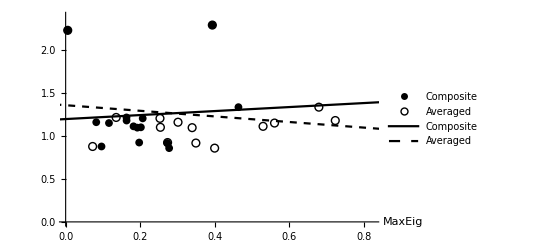

Composite P Value: {0.824959}       Averaged P Value: {0.58194}

Composite Correlation: 0.0624704     Averaged Correlation: -0.154714

Composite R-Squared: 0.00390255      Averaged R-Squared: 0.0239363

```mathematica
lmRSquaredListFunction2[realCCV,MaxEig,True]
```

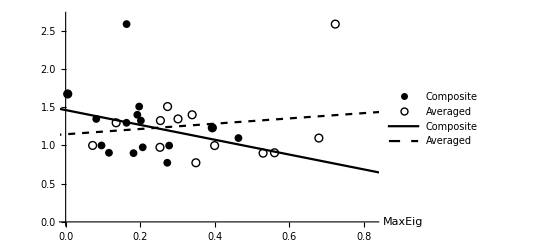

Composite P Value: {0.359161}       Averaged P Value: {0.567111}

Composite Correlation: -0.25493     Averaged Correlation: 0.160749

Composite R-Squared: 0.0649894      Averaged R-Squared: 0.0258404

```mathematica
lmRSquaredListFunction2[realHCCV,MaxEig,True](* no algae *)
```

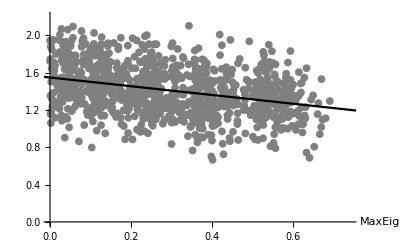

Composite P Value: {1.68768×10^-27}

Composite Correlation: -0.334087

Composite R-Squared: 0.111614

```mathematica
lmRSquaredListFunctionGen[genCCVrange,MaxEig,True,genbrange]
```

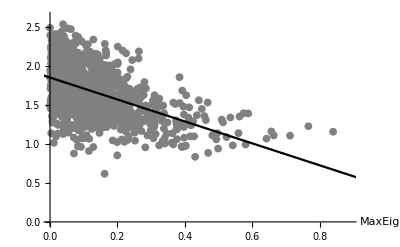

Composite P Value: {2.15184×10^-63}

Composite Correlation: -0.496616

Composite R-Squared: 0.246627

```mathematica
lmRSquaredListFunctionGen[genCCV,MaxEig,True]
```

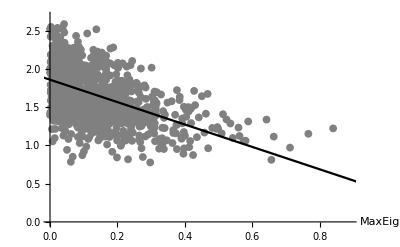

Composite P Value: {9.02558×10^-64}

Composite Correlation: -0.49793

Composite R-Squared: 0.247934

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,MaxEig,True] (* with covariates *)
```

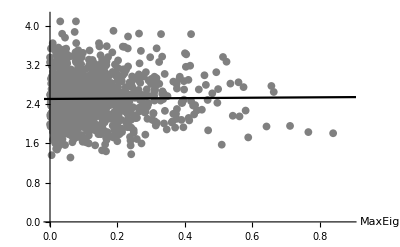

Composite P Value: {0.735351}

Composite Correlation: 0.0107021

Composite R-Squared: 0.000114534

```mathematica
lmRSquaredListFunctionGen[genHCCVrange,MaxEig,True]
```

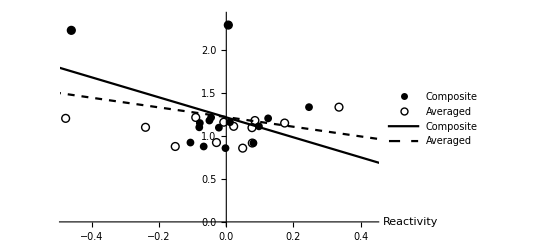

Composite P Value: {0.128189}       Averaged P Value: {0.307216}

Composite Correlation: -0.410851     Averaged Correlation: -0.282741

Composite R-Squared: 0.168798      Averaged R-Squared: 0.0799426

```mathematica
lmRSquaredListFunction2[realCCV,Reactivity,True]
```

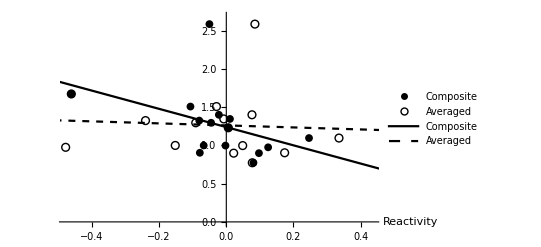

Composite P Value: {0.126577}       Averaged P Value: {0.818119}

Composite Correlation: -0.412437     Averaged Correlation: -0.0649488

Composite R-Squared: 0.170105      Averaged R-Squared: 0.00421834

```mathematica
lmRSquaredListFunction2[realHCCV,Reactivity,True](* no algae *)
```

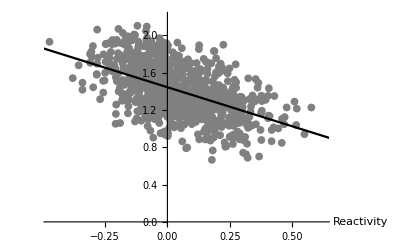

Composite P Value: {1.33714×10^-67}

Composite Correlation: -0.510949

Composite R-Squared: 0.261068

```mathematica
lmRSquaredListFunctionGen[genCCVrange,Reactivity,True,genbrange]
```

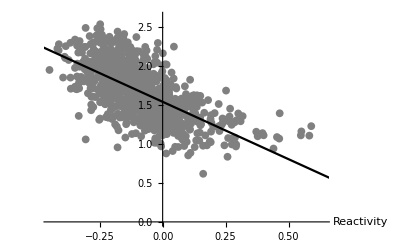

Composite P Value: {2.85165×10^-120}

Composite Correlation: -0.64825

Composite R-Squared: 0.420229

```mathematica
lmRSquaredListFunctionGen[genCCV,Reactivity,True]
```

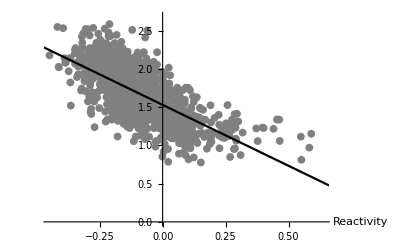

Composite P Value: {1.44748×10^-134}

Composite Correlation: -0.676159

Composite R-Squared: 0.457191

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,Reactivity,True](* with covariates *)
```

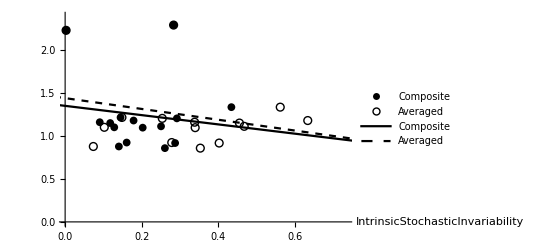

Composite P Value: {0.642273}       Averaged P Value: {0.350611}

Composite Correlation: -0.130767     Averaged Correlation: -0.259344

Composite R-Squared: 0.0170999      Averaged R-Squared: 0.0672593

```mathematica
lmRSquaredListFunction2[realCCV,IntrinsicStochasticInvariability,True]
```

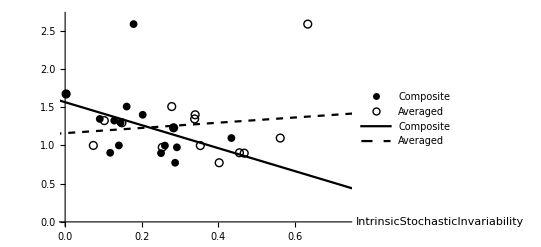

Composite P Value: {0.192223}       Averaged P Value: {0.6242}

Composite Correlation: -0.356432     Averaged Correlation: 0.137845

Composite R-Squared: 0.127044      Averaged R-Squared: 0.0190013

```mathematica
lmRSquaredListFunction2[realHCCV,IntrinsicStochasticInvariability,True](* no algae *)
```

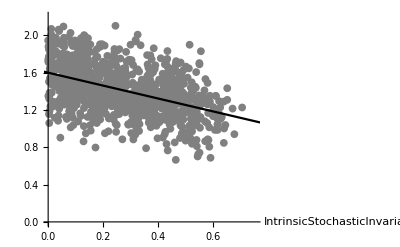

Composite P Value: {1.00899×10^-52}

Composite Correlation: -0.456874

Composite R-Squared: 0.208734

```mathematica
lmRSquaredListFunctionGen[genCCVrange,IntrinsicStochasticInvariability,True,genbrange]
```

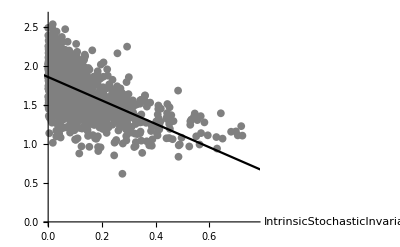

Composite P Value: {5.07734×10^-91}

Composite Correlation: -0.580168

Composite R-Squared: 0.336594

```mathematica
lmRSquaredListFunctionGen[genCCV,IntrinsicStochasticInvariability,True]
```

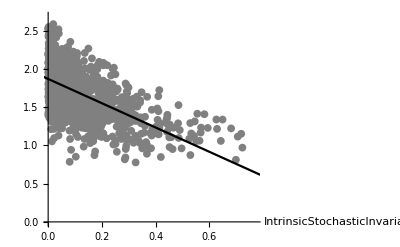

Composite P Value: {3.47169×10^-95}

Composite Correlation: -0.590931

Composite R-Squared: 0.349199

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,IntrinsicStochasticInvariability,True](* with covariates *)
```

### Weighted Averaged CV

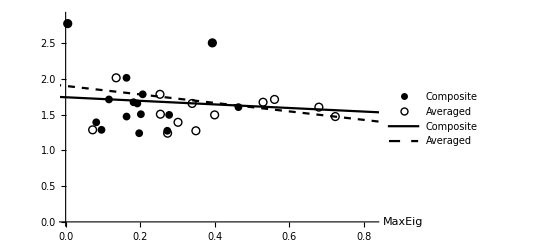

Composite P Value: {0.813641}       Averaged P Value: {0.313917}

Composite Correlation: -0.0665739     Averaged Correlation: -0.27901

Composite R-Squared: 0.00443208      Averaged R-Squared: 0.0778465

```mathematica
lmRSquaredListFunction2[realWPCV,MaxEig,True]
```

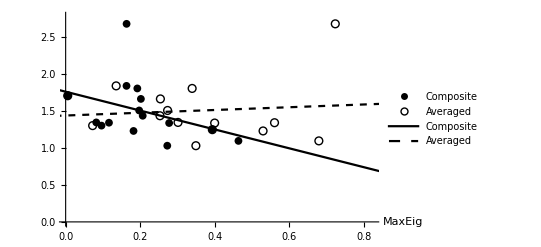

Composite P Value: {0.178258}       Averaged P Value: {0.736415}

Composite Correlation: -0.367137     Averaged Correlation: 0.0949519

Composite R-Squared: 0.134789      Averaged R-Squared: 0.00901586

```mathematica
lmRSquaredListFunction2[realHWPCV,MaxEig,True](* no algae *)
```

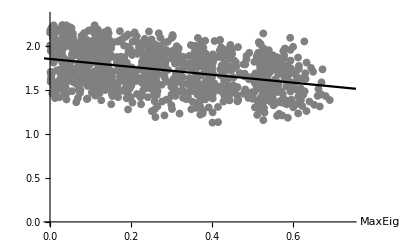

Composite P Value: {2.16489×10^-31}

Composite Correlation: -0.356809

Composite R-Squared: 0.127312

```mathematica
lmRSquaredListFunctionGen[genWPCVrange,MaxEig,True,genbrange]
```

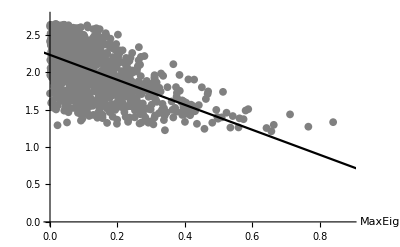

Composite P Value: {1.81027×10^-87}

Composite Correlation: -0.57066

Composite R-Squared: 0.325653

```mathematica
lmRSquaredListFunctionGen[genWPCV,MaxEig,True]
```

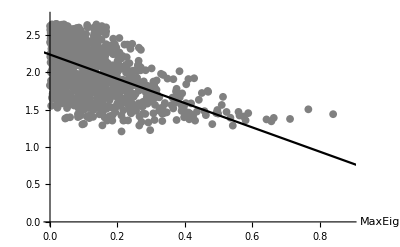

Composite P Value: {3.55935×10^-81}

Composite Correlation: -0.553015

Composite R-Squared: 0.305826

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,MaxEig,True](* with covariates *)
```

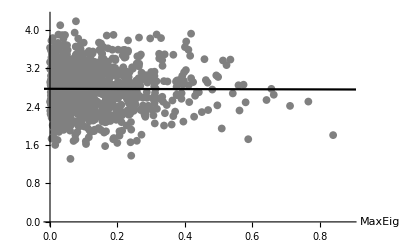

Composite P Value: {0.898467}

Composite Correlation: -0.00404004

Composite R-Squared: 0.0000163219

```mathematica
lmRSquaredListFunctionGen[genHWPCVrange,MaxEig,True]
```

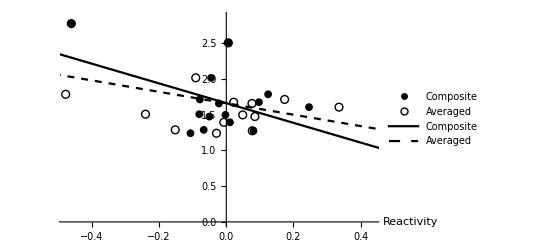

Composite P Value: {0.0686778}       Averaged P Value: {0.142491}

Composite Correlation: -0.482252     Averaged Correlation: -0.397342

Composite R-Squared: 0.232567      Averaged R-Squared: 0.157881

```mathematica
lmRSquaredListFunction2[realWPCV,Reactivity,True]
```

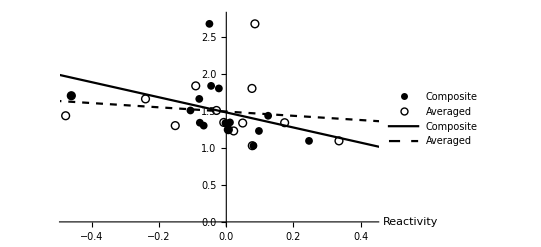

Composite P Value: {0.154408}       Averaged P Value: {0.582372}

Composite Correlation: -0.386768     Averaged Correlation: -0.154539

Composite R-Squared: 0.149589      Averaged R-Squared: 0.0238823

```mathematica
lmRSquaredListFunction2[realHWPCV,Reactivity,True](* no algae *)
```

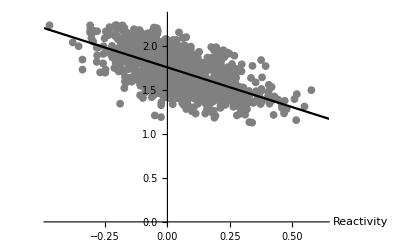

Composite P Value: {1.81398×10^-104}

Composite Correlation: -0.613545

Composite R-Squared: 0.376438

```mathematica
lmRSquaredListFunctionGen[genWPCVrange,Reactivity,True,genbrange]
```

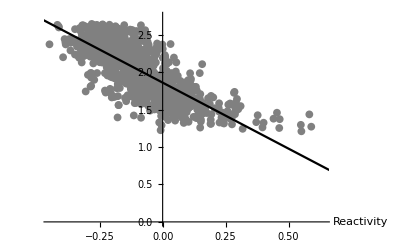

Composite P Value: {7.74096×10^-184}

Composite Correlation: -0.753317

Composite R-Squared: 0.567486

```mathematica
lmRSquaredListFunctionGen[genWPCV,Reactivity,True]
```

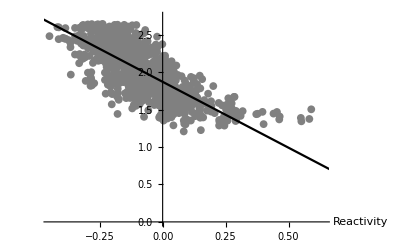

Composite P Value: {3.93014×10^-181}

Composite Correlation: -0.749705

Composite R-Squared: 0.562057

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,Reactivity,True](* with covariates *)
```

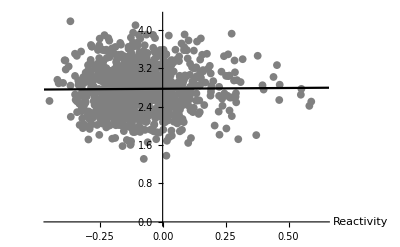

Composite P Value: {0.739264}

Composite Correlation: 0.0105378

Composite R-Squared: 0.000111046

```mathematica
lmRSquaredListFunctionGen[genHWPCVrange,Reactivity,True]
```

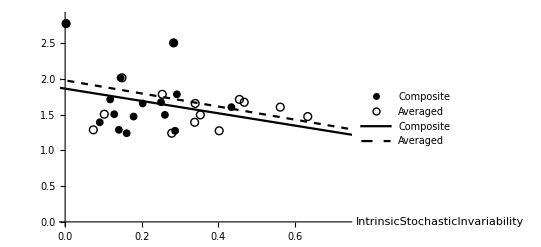

Composite P Value: {0.460025}       Averaged P Value: {0.170286}

Composite Correlation: -0.20661     Averaged Correlation: -0.373494

Composite R-Squared: 0.0426877      Averaged R-Squared: 0.139498

```mathematica
lmRSquaredListFunction2[realWPCV,IntrinsicStochasticInvariability,True]
```

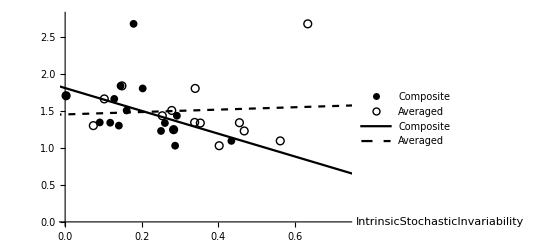

Composite P Value: {0.138856}       Averaged P Value: {0.800417}

Composite Correlation: -0.400684     Averaged Correlation: 0.0713844

Composite R-Squared: 0.160548      Averaged R-Squared: 0.00509573

```mathematica
lmRSquaredListFunction2[realHWPCV,IntrinsicStochasticInvariability,True](* no algae *)
```

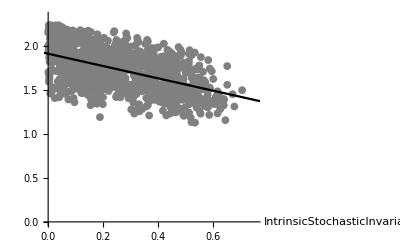

Composite P Value: {1.07357×10^-68}

Composite Correlation: -0.514571

Composite R-Squared: 0.264784

```mathematica
lmRSquaredListFunctionGen[genWPCVrange,IntrinsicStochasticInvariability,True,genbrange]
```

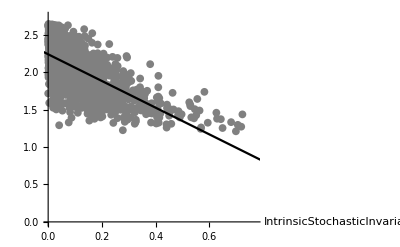

Composite P Value: {2.87572×10^-130}

Composite Correlation: -0.66808

Composite R-Squared: 0.446331

```mathematica
lmRSquaredListFunctionGen[genWPCV,IntrinsicStochasticInvariability,True]
```

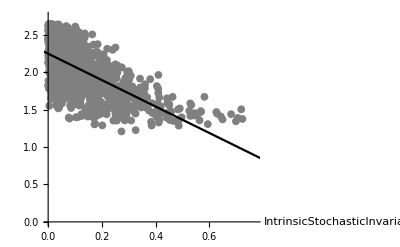

Composite P Value: {5.48615×10^-126}

Composite Correlation: -0.659773

Composite R-Squared: 0.4353

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,IntrinsicStochasticInvariability,True](* with covariates *)
```

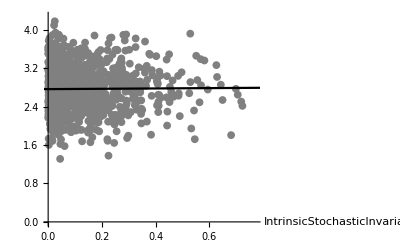

Composite P Value: {0.7579}

Composite Correlation: 0.00975938

Composite R-Squared: 0.0000952455

```mathematica
lmRSquaredListFunctionGen[genHWPCVrange,IntrinsicStochasticInvariability,True]
```

### Mean CV

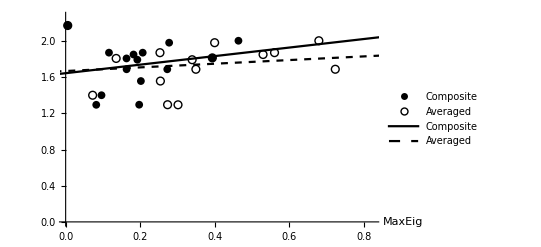

Composite P Value: {0.442002}       Averaged P Value: {0.562271}

Composite Correlation: 0.214809     Averaged Correlation: 0.162734

Composite R-Squared: 0.0461428      Averaged R-Squared: 0.0264823

```mathematica
lmRSquaredListFunction2[realPCV,MaxEig,True]
```

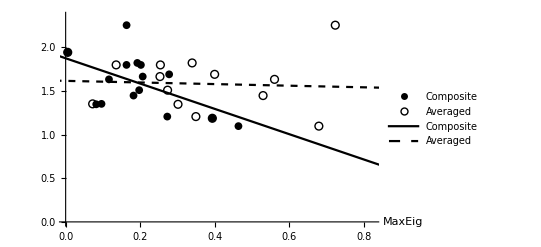

Composite P Value: {0.0411762}       Averaged P Value: {0.83184}

Composite Correlation: -0.532104     Averaged Correlation: -0.059981

Composite R-Squared: 0.283135      Averaged R-Squared: 0.00359772

```mathematica
lmRSquaredListFunction2[realHPCV,MaxEig,True](* no algae *)
```

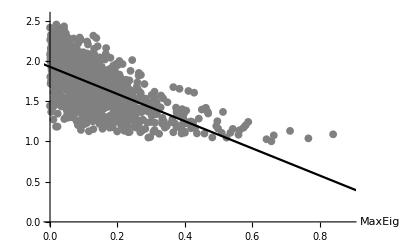

Composite P Value: {9.49179×10^-109}

Composite Correlation: -0.623391

Composite R-Squared: 0.388617

```mathematica
lmRSquaredListFunctionGen[genPCV,MaxEig,True]
```

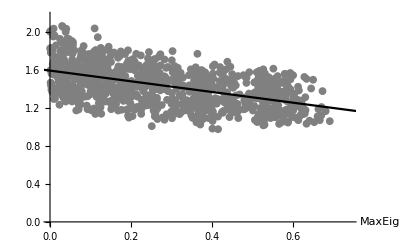

Composite P Value: {1.50598×10^-67}

Composite Correlation: -0.510777

Composite R-Squared: 0.260893

```mathematica
lmRSquaredListFunctionGen[genPCVrange,MaxEig,True,genbrange]
```

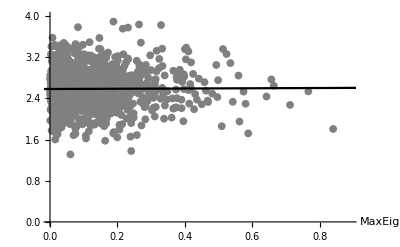

Composite P Value: {0.812189}

Composite Correlation: 0.00752295

Composite R-Squared: 0.0000565948

```mathematica
lmRSquaredListFunctionGen[genHPCVrange,MaxEig,True]
```

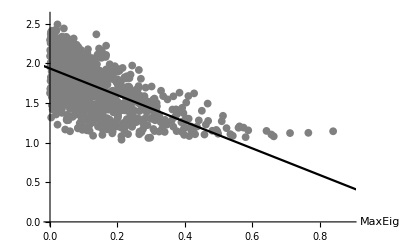

Composite P Value: {9.85379×10^-108}

Composite Correlation: -0.621086

Composite R-Squared: 0.385747

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,MaxEig,True](* with covariates *)
```

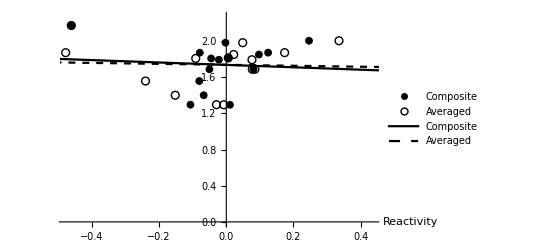

Composite P Value: {0.77869}       Averaged P Value: {0.873317}

Composite Correlation: -0.0793284     Averaged Correlation: -0.0450574

Composite R-Squared: 0.006293      Averaged R-Squared: 0.00203017

```mathematica
lmRSquaredListFunction2[realPCV,Reactivity,True]
```

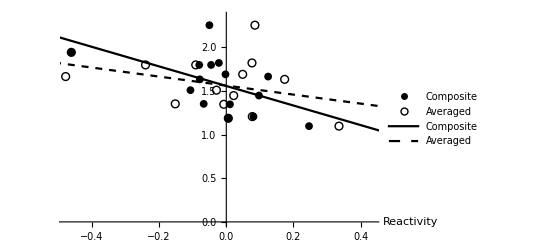

Composite P Value: {0.0370991}       Averaged P Value: {0.194413}

Composite Correlation: -0.54147     Averaged Correlation: -0.3548

Composite R-Squared: 0.29319      Averaged R-Squared: 0.125883

```mathematica
lmRSquaredListFunction2[realHPCV,Reactivity,True](* no algae *)
```

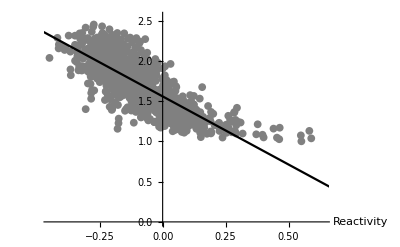

Composite P Value: {1.28195×10^-205}

Composite Correlation: -0.780267

Composite R-Squared: 0.608816

```mathematica
lmRSquaredListFunctionGen[genPCV,Reactivity,True]
```

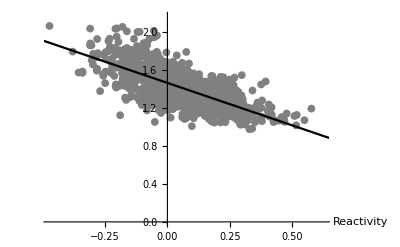

Composite P Value: {2.15642×10^-144}

Composite Correlation: -0.693706

Composite R-Squared: 0.481228

```mathematica
lmRSquaredListFunctionGen[genPCVrange,Reactivity,True,genbrange]
```

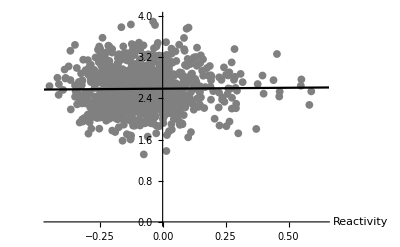

Composite P Value: {0.660489}

Composite Correlation: 0.0139066

Composite R-Squared: 0.000193395

```mathematica
lmRSquaredListFunctionGen[genHPCVrange,Reactivity,True]
```

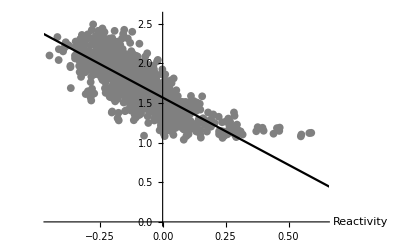

Composite P Value: {1.30107×10^-208}

Composite Correlation: -0.783696

Composite R-Squared: 0.614179

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,Reactivity,True](* with covariates *)
```

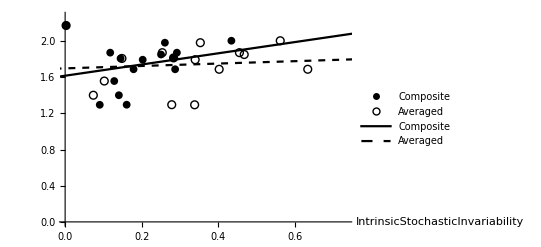

Composite P Value: {0.359812}       Averaged P Value: {0.742839}

Composite Correlation: 0.254596     Averaged Correlation: 0.092562

Composite R-Squared: 0.0648193      Averaged R-Squared: 0.00856772

```mathematica
lmRSquaredListFunction2[realPCV,IntrinsicStochasticInvariability,True]
```

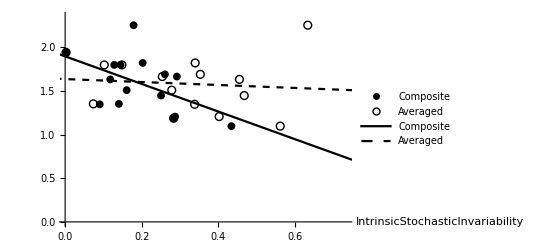

Composite P Value: {0.0449433}       Averaged P Value: {0.734378}

Composite Correlation: -0.524045     Averaged Correlation: -0.0957109

Composite R-Squared: 0.274623      Averaged R-Squared: 0.00916057

```mathematica
lmRSquaredListFunction2[realHPCV,IntrinsicStochasticInvariability,True](* no algae *)
```

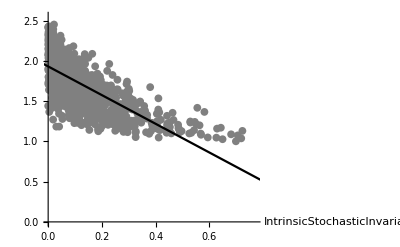

Composite P Value: {6.06599×10^-161}

Composite Correlation: -0.72065

Composite R-Squared: 0.519336

```mathematica
lmRSquaredListFunctionGen[genPCV,IntrinsicStochasticInvariability,True]
```

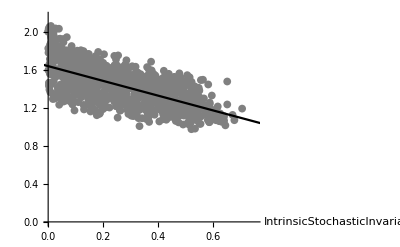

Composite P Value: {1.51986×10^-122}

Composite Correlation: -0.652894

Composite R-Squared: 0.42627

```mathematica
lmRSquaredListFunctionGen[genPCVrange,IntrinsicStochasticInvariability,True,genbrange]
```

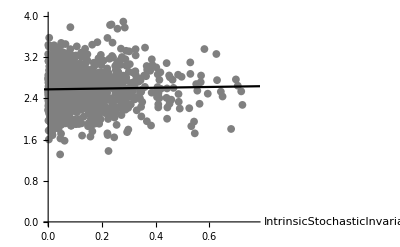

Composite P Value: {0.403975}

Composite Correlation: 0.026419

Composite R-Squared: 0.000697964

```mathematica
lmRSquaredListFunctionGen[genHPCVrange,IntrinsicStochasticInvariability,True]
```

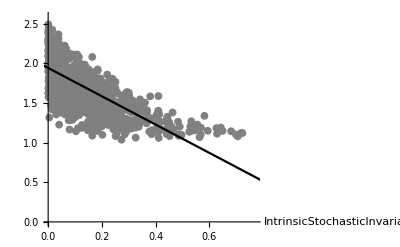

Composite P Value: {1.45354×10^-162}

Composite Correlation: -0.723128

Composite R-Squared: 0.522914

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,IntrinsicStochasticInvariability,True](* with covariates *)
```

## 2. Empirical vs. Interaction Strength

### CCV

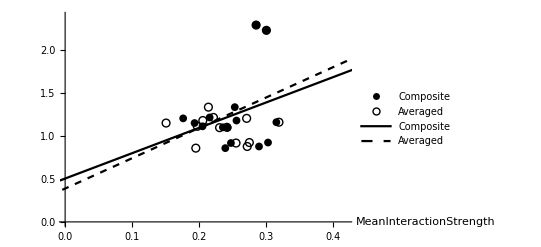

Composite P Value: {0.303708}       Averaged P Value: {0.171734}

Composite Correlation: 0.284713     Averaged Correlation: 0.372325

Composite R-Squared: 0.0810616      Averaged R-Squared: 0.138626

```mathematica
lmRSquaredListFunction2[realCCV,MeanInteractionStrength,True]
```

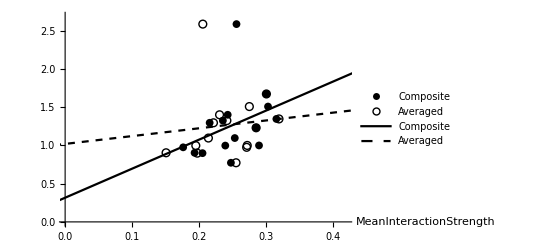

Composite P Value: {0.188908}       Averaged P Value: {0.708154}

Composite Correlation: 0.358926     Averaged Correlation: 0.105538

Composite R-Squared: 0.128828      Averaged R-Squared: 0.0111384

```mathematica
lmRSquaredListFunction2[realHCCV,MeanInteractionStrength,True](* no algae *)
```

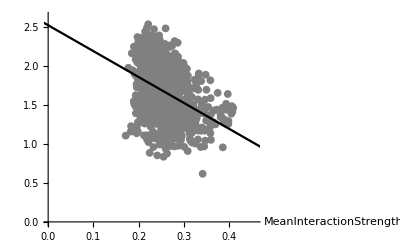

Composite P Value: {5.23376×10^-42}

Composite Correlation: -0.410856

Composite R-Squared: 0.168803

```mathematica
lmRSquaredListFunctionGen[genCCV,MeanInteractionStrength,True]
```

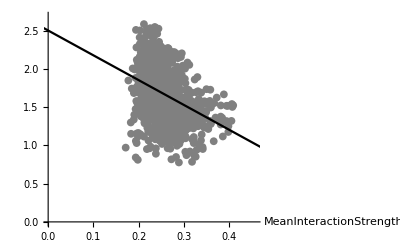

Composite P Value: {5.23521×10^-37}

Composite Correlation: -0.386658

Composite R-Squared: 0.149504

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,MeanInteractionStrength,True](* with covariates *)
```

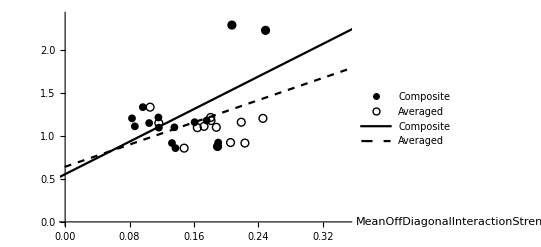

Composite P Value: {0.0426156}       Averaged P Value: {0.261897}

Composite Correlation: 0.528962     Averaged Correlation: 0.309337

Composite R-Squared: 0.279801      Averaged R-Squared: 0.0956893

```mathematica
lmRSquaredListFunction2[realCCV,MeanOffDiagonalInteractionStrength,True]
```

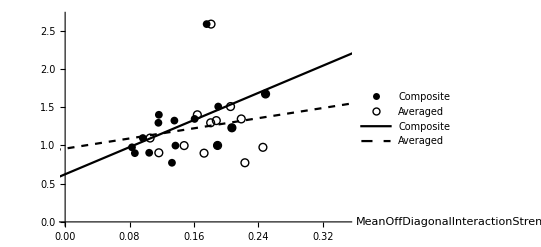

Composite P Value: {0.0668981}       Averaged P Value: {0.579818}

Composite Correlation: 0.484982     Averaged Correlation: 0.155573

Composite R-Squared: 0.235207      Averaged R-Squared: 0.024203

```mathematica
lmRSquaredListFunction2[realHCCV,MeanOffDiagonalInteractionStrength,True](* no algae *)
```

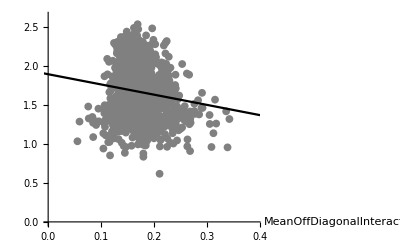

Composite P Value: {4.66101×10^-6}

Composite Correlation: -0.144239

Composite R-Squared: 0.0208048

```mathematica
lmRSquaredListFunctionGen[genCCV,MeanOffDiagonalInteractionStrength,True]
```

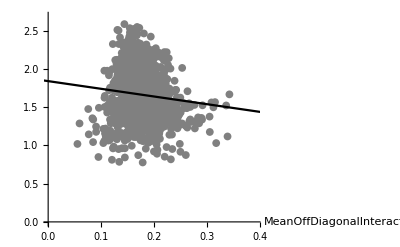

Composite P Value: {0.000741486}

Composite Correlation: -0.106517

Composite R-Squared: 0.0113459

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,MeanOffDiagonalInteractionStrength,True](* with covariates *)
```

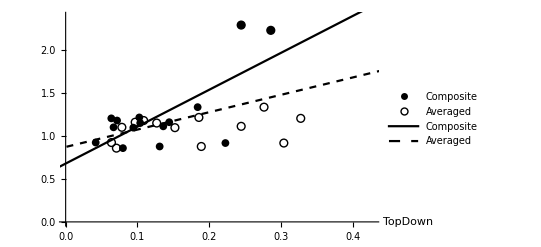

Composite P Value: {0.00261374}       Averaged P Value: {0.113921}

Composite Correlation: 0.71724     Averaged Correlation: 0.425398

Composite R-Squared: 0.514434      Averaged R-Squared: 0.180963

```mathematica
lmRSquaredListFunction2[realCCV,TopDown,True]
```

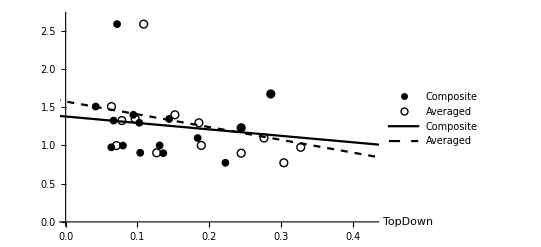

Composite P Value: {0.624044}       Averaged P Value: {0.209554}

Composite Correlation: -0.137907     Averaged Correlation: -0.343825

Composite R-Squared: 0.0190182      Averaged R-Squared: 0.118215

```mathematica
lmRSquaredListFunction2[realHCCV,TopDown,True](* no algae *)
```

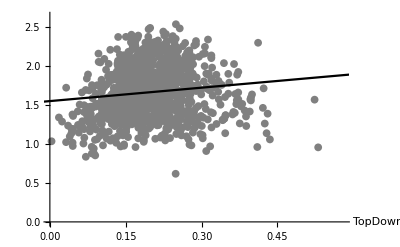

Composite P Value: {0.0000822162}

Composite Correlation: 0.124199

Composite R-Squared: 0.0154253

```mathematica
lmRSquaredListFunctionGen[genCCV,TopDown,True]
```

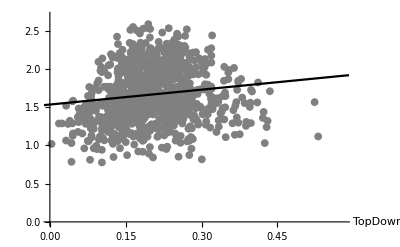

Composite P Value: {0.0000174785}

Composite Correlation: 0.13536

Composite R-Squared: 0.0183223

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,TopDown,True](* with covariates *)
```

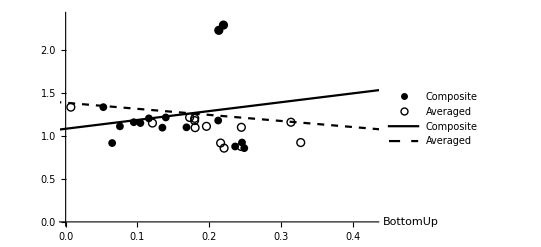

Composite P Value: {0.556482}       Averaged P Value: {0.663675}

Composite Correlation: 0.165116     Averaged Correlation: -0.122478

Composite R-Squared: 0.0272634      Averaged R-Squared: 0.0150008

```mathematica
lmRSquaredListFunction2[realCCV,BottomUp,True]
```

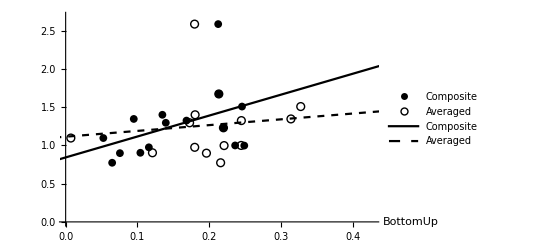

Composite P Value: {0.11027}       Averaged P Value: {0.647963}

Composite Correlation: 0.42932     Averaged Correlation: 0.128553

Composite R-Squared: 0.184315      Averaged R-Squared: 0.016526

```mathematica
lmRSquaredListFunction2[realHCCV,BottomUp,True](* no algae *)
```

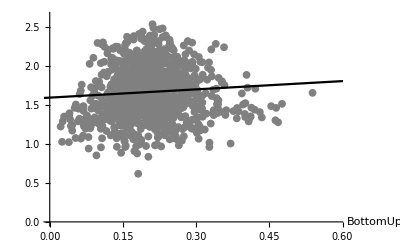

Composite P Value: {0.0162102}

Composite Correlation: 0.0760109

Composite R-Squared: 0.00577766

```mathematica
lmRSquaredListFunctionGen[genCCV,BottomUp,True]
```

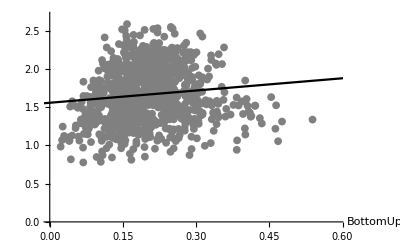

Composite P Value: {0.000449178}

Composite Correlation: 0.110773

Composite R-Squared: 0.0122706

```mathematica
lmRSquaredListFunctionGen[genCCVwithC,BottomUp,True](* with covariates *)
```

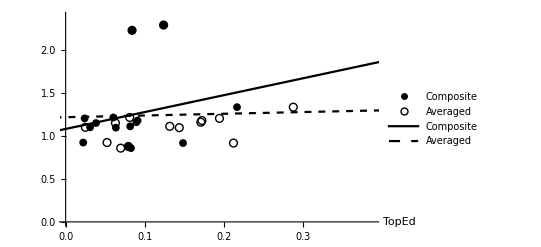

Composite P Value: {0.406809}       Averaged P Value: {0.907545}

Composite Correlation: 0.231322     Averaged Correlation: 0.032826

Composite R-Squared: 0.0535097      Averaged R-Squared: 0.00107755

```mathematica
lmRSquaredListFunction2[realCCV,TopEd,True]
```

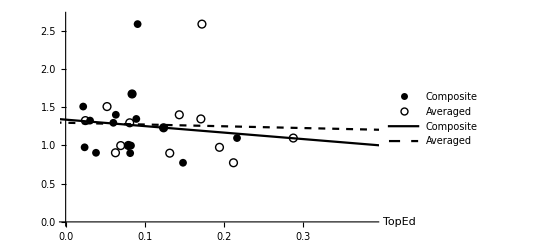

Composite P Value: {0.72941}       Averaged P Value: {0.895405}

Composite Correlation: -0.0975644     Averaged Correlation: -0.0371569

Composite R-Squared: 0.00951882      Averaged R-Squared: 0.00138064

```mathematica
lmRSquaredListFunction2[realHCCV,TopEd,True]
```

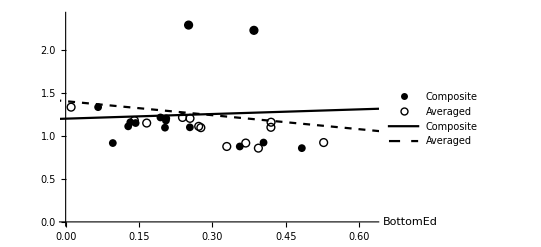

Composite P Value: {0.857061}       Averaged P Value: {0.561626}

Composite Correlation: 0.0508912     Averaged Correlation: -0.162998

Composite R-Squared: 0.00258991      Averaged R-Squared: 0.0265685

```mathematica
lmRSquaredListFunction2[realCCV,BottomEd,True]
```

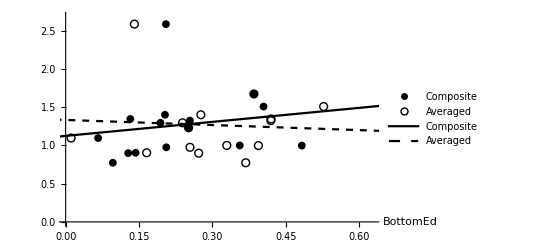

Composite P Value: {0.547929}       Averaged P Value: {0.817392}

Composite Correlation: 0.168657     Averaged Correlation: -0.0652126

Composite R-Squared: 0.0284451      Averaged R-Squared: 0.00425268

```mathematica
lmRSquaredListFunction2[realHCCV,BottomEd,True]
```

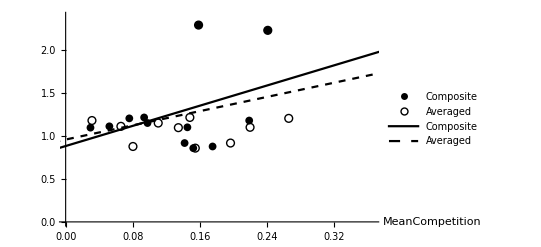

Composite P Value: {0.205903}       Averaged P Value: {0.327077}

Composite Correlation: 0.393323     Averaged Correlation: 0.309823

Composite R-Squared: 0.154703      Averaged R-Squared: 0.0959905

```mathematica
lmRSquaredListFunction2[realCCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),MeanCompetition,True,realCCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),{19,20,22,24,25,26,27,28,29,30,31,32}]
```

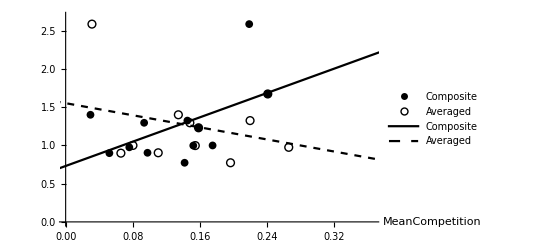

Composite P Value: {0.0843183}       Averaged P Value: {0.364104}

Composite Correlation: 0.518262     Averaged Correlation: -0.287945

Composite R-Squared: 0.268596      Averaged R-Squared: 0.0829124

```mathematica
lmRSquaredListFunction2[realHCCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),MeanCompetition,True,realHCCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),{19,20,22,24,25,26,27,28,29,30,31,32}](* no algae *)
```

### Weighted Average CV

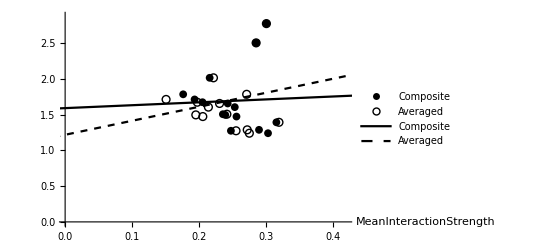

Composite P Value: {0.890688}       Averaged P Value: {0.46463}

Composite Correlation: 0.038842     Averaged Correlation: 0.204541

Composite R-Squared: 0.0015087      Averaged R-Squared: 0.041837

```mathematica
lmRSquaredListFunction2[realWPCV,MeanInteractionStrength,True]
```

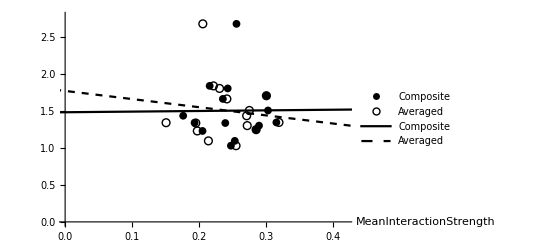

Composite P Value: {0.975189}       Averaged P Value: {0.658089}

Composite Correlation: 0.0087929     Averaged Correlation: -0.124632

Composite R-Squared: 0.000077315      Averaged R-Squared: 0.015533

```mathematica
lmRSquaredListFunction2[realHWPCV,MeanInteractionStrength,True](* no algae *)
```

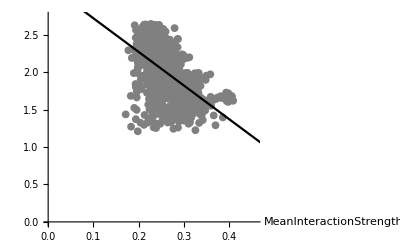

Composite P Value: {2.25141×10^-76}

Composite Correlation: -0.538806

Composite R-Squared: 0.290312

```mathematica
lmRSquaredListFunctionGen[genWPCV,MeanInteractionStrength,True]
```

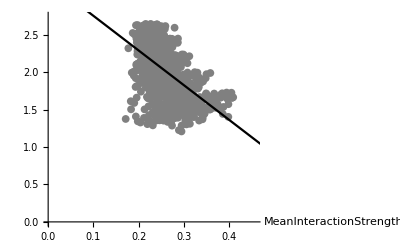

Composite P Value: {1.44186×10^-81}

Composite Correlation: -0.554147

Composite R-Squared: 0.307079

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,MeanInteractionStrength,True](* with covariates *)
```

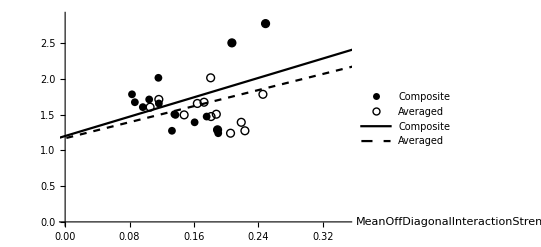

Composite P Value: {0.169154}       Averaged P Value: {0.337324}

Composite Correlation: 0.374412     Averaged Correlation: 0.266324

Composite R-Squared: 0.140185      Averaged R-Squared: 0.0709284

```mathematica
lmRSquaredListFunction2[realWPCV,MeanOffDiagonalInteractionStrength,True]
```

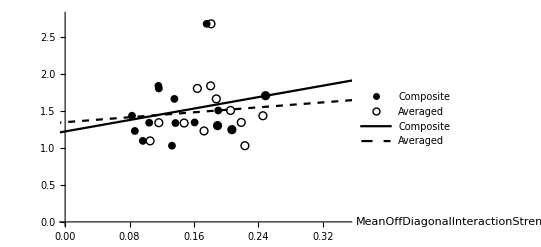

Composite P Value: {0.406171}       Averaged P Value: {0.760785}

Composite Correlation: 0.231628     Averaged Correlation: 0.0859171

Composite R-Squared: 0.0536515      Averaged R-Squared: 0.00738175

```mathematica
lmRSquaredListFunction2[realHWPCV,MeanOffDiagonalInteractionStrength,True](* no algae *)
```

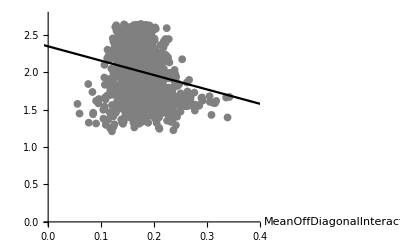

Composite P Value: {6.54936×10^-11}

Composite Correlation: -0.204584

Composite R-Squared: 0.0418548

```mathematica
lmRSquaredListFunctionGen[genWPCV,MeanOffDiagonalInteractionStrength,True]
```

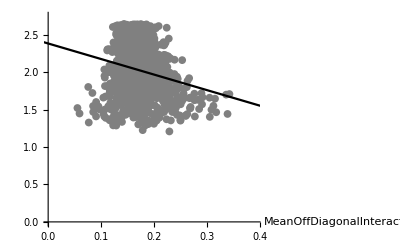

Composite P Value: {1.62627×10^-12}

Composite Correlation: -0.220872

Composite R-Squared: 0.0487846

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,MeanOffDiagonalInteractionStrength,True](* with covariates *)
```

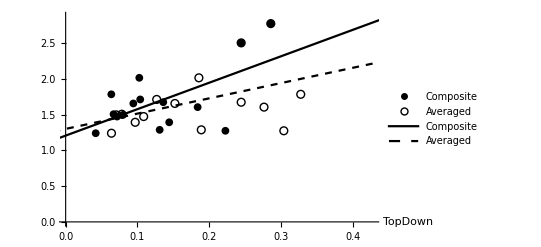

Composite P Value: {0.0154502}       Averaged P Value: {0.0966721}

Composite Correlation: 0.611375     Averaged Correlation: 0.444778

Composite R-Squared: 0.373779      Averaged R-Squared: 0.197827

```mathematica
lmRSquaredListFunction2[realWPCV,TopDown,True]
```

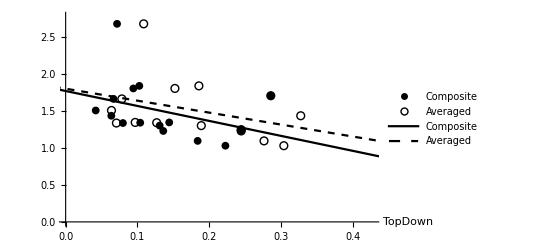

Composite P Value: {0.184623}       Averaged P Value: {0.181592}

Composite Correlation: -0.362192     Averaged Correlation: -0.364533

Composite R-Squared: 0.131183      Averaged R-Squared: 0.132884

```mathematica
lmRSquaredListFunction2[realHWPCV,TopDown,True](* no algae *)
```

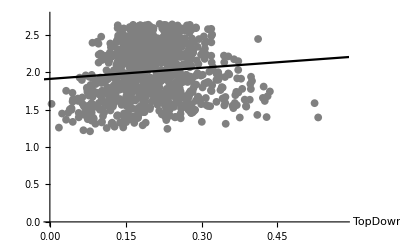

Composite P Value: {0.00103444}

Composite Correlation: 0.103604

Composite R-Squared: 0.0107338

```mathematica
lmRSquaredListFunctionGen[genWPCV,TopDown,True]
```

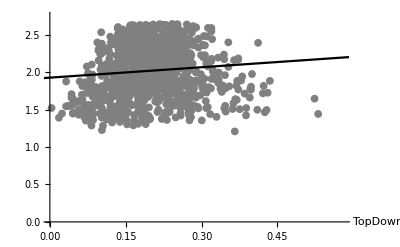

Composite P Value: {0.00213025}

Composite Correlation: 0.0970198

Composite R-Squared: 0.00941283

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,TopDown,True](* with covariates *)
```

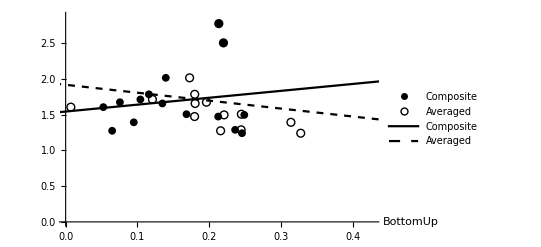

Composite P Value: {0.585979}       Averaged P Value: {0.496269}

Composite Correlation: 0.153081     Averaged Correlation: -0.190584

Composite R-Squared: 0.0234337      Averaged R-Squared: 0.0363223

```mathematica
lmRSquaredListFunction2[realWPCV,BottomUp,True]
```

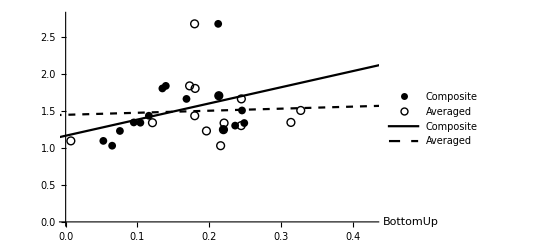

Composite P Value: {0.168117}       Averaged P Value: {0.855297}

Composite Correlation: 0.375257     Averaged Correlation: 0.0515254

Composite R-Squared: 0.140818      Averaged R-Squared: 0.00265487

```mathematica
lmRSquaredListFunction2[realHWPCV,BottomUp,True](* no algae *)
```

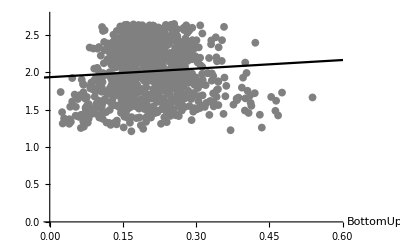

Composite P Value: {0.0116373}

Composite Correlation: 0.0797555

Composite R-Squared: 0.00636094

```mathematica
lmRSquaredListFunctionGen[genWPCV,BottomUp,True]
```

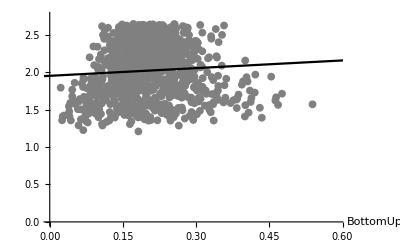

Composite P Value: {0.0241806}

Composite Correlation: 0.071284

Composite R-Squared: 0.00508141

```mathematica
lmRSquaredListFunctionGen[genWPCVwithC,BottomUp,True](* with covariates *)
```

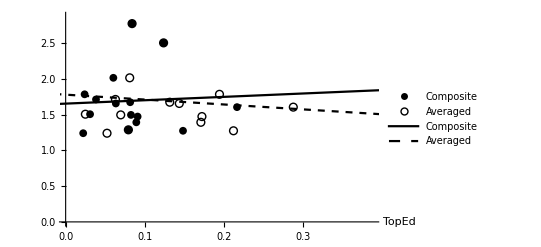

Composite P Value: {0.845546}       Averaged P Value: {0.691934}

Composite Correlation: 0.0550351     Averaged Correlation: -0.111674

Composite R-Squared: 0.00302886      Averaged R-Squared: 0.012471

```mathematica
lmRSquaredListFunction2[realWPCV,TopEd,True]
```

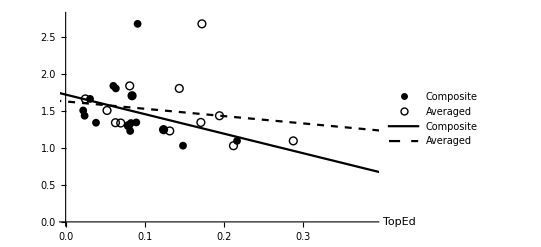

Composite P Value: {0.224756}       Averaged P Value: {0.534166}

Composite Correlation: -0.333302     Averaged Correlation: -0.174404

Composite R-Squared: 0.11109      Averaged R-Squared: 0.0304169

```mathematica
lmRSquaredListFunction2[realHWPCV,TopEd,True]
```

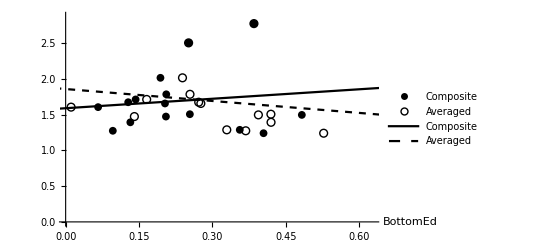

Composite P Value: {0.661842}       Averaged P Value: {0.556107}

Composite Correlation: 0.123184     Averaged Correlation: -0.165271

Composite R-Squared: 0.0151743      Averaged R-Squared: 0.0273146

```mathematica
lmRSquaredListFunction2[realWPCV,BottomEd,True]
```

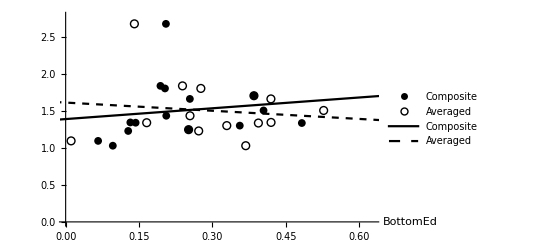

Composite P Value: {0.601277}       Averaged P Value: {0.674077}

Composite Correlation: 0.146937     Averaged Correlation: -0.118483

Composite R-Squared: 0.0215905      Averaged R-Squared: 0.0140382

```mathematica
lmRSquaredListFunction2[realHWPCV,BottomEd,True]
```

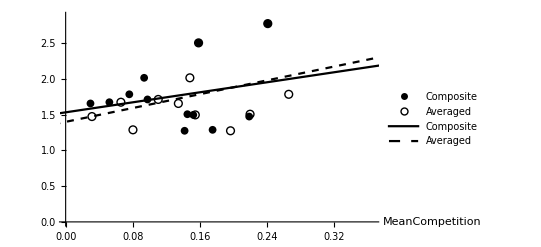

Composite P Value: {0.445414}       Averaged P Value: {0.22842}

Composite Correlation: 0.243637     Averaged Correlation: 0.375962

Composite R-Squared: 0.059359      Averaged R-Squared: 0.141348

```mathematica
lmRSquaredListFunction2[realWPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),MeanCompetition,True,realWPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),{19,20,22,24,25,26,27,28,29,30,31,32}]
```

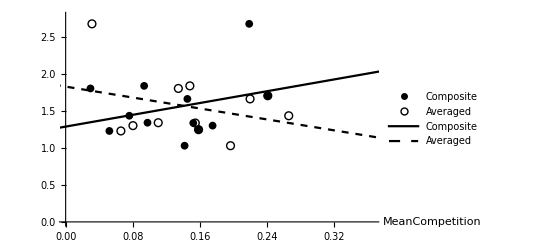

Composite P Value: {0.35409}       Averaged P Value: {0.335608}

Composite Correlation: 0.29374     Averaged Correlation: -0.304669

Composite R-Squared: 0.0862832      Averaged R-Squared: 0.0928231

```mathematica
lmRSquaredListFunction2[realHWPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),MeanCompetition,True,realHWPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),{19,20,22,24,25,26,27,28,29,30,31,32}](* no algae *)
```

### Mean CV

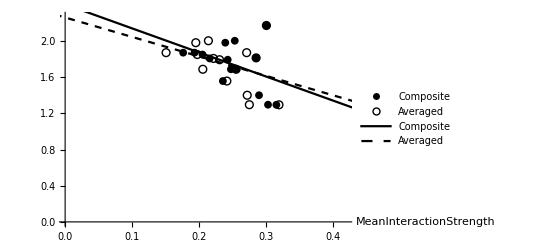

Composite P Value: {0.10487}       Averaged P Value: {0.157446}

Composite Correlation: -0.43529     Averaged Correlation: -0.38416

Composite R-Squared: 0.189478      Averaged R-Squared: 0.147579

```mathematica
lmRSquaredListFunction2[realPCV,MeanInteractionStrength,True]
```

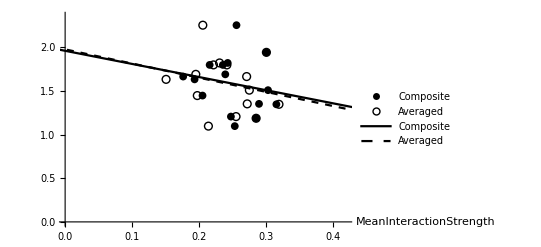

Composite P Value: {0.477908}       Averaged P Value: {0.401416}

Composite Correlation: -0.19863     Averaged Correlation: -0.233917

Composite R-Squared: 0.0394538      Averaged R-Squared: 0.0547172

```mathematica
lmRSquaredListFunction2[realHPCV,MeanInteractionStrength,True](* no algae *)
```

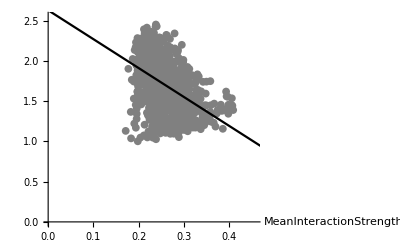

Composite P Value: {8.97312×10^-55}

Composite Correlation: -0.46493

Composite R-Squared: 0.216159

```mathematica
lmRSquaredListFunctionGen[genPCV,MeanInteractionStrength,True]
```

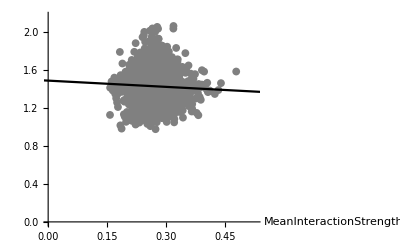

Composite P Value: {0.0989316}

Composite Correlation: -0.0522091

Composite R-Squared: 0.00272579

```mathematica
lmRSquaredListFunctionGen[genPCVrange,MeanInteractionStrength,True,genbrange]
```

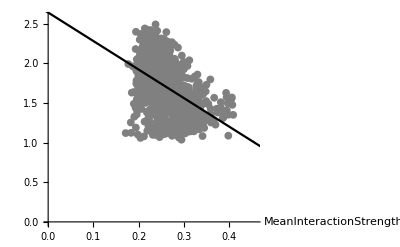

Composite P Value: {3.85698×10^-55}

Composite Correlation: -0.466347

Composite R-Squared: 0.21748

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,MeanInteractionStrength,True](* with covariates *)
```

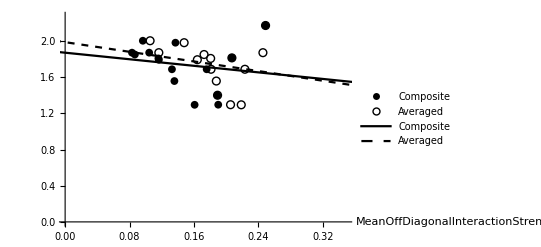

Composite P Value: {0.540984}       Averaged P Value: {0.439069}

Composite Correlation: -0.171549     Averaged Correlation: -0.216159

Composite R-Squared: 0.0294291      Averaged R-Squared: 0.0467245

```mathematica
lmRSquaredListFunction2[realPCV,MeanOffDiagonalInteractionStrength,True]
```

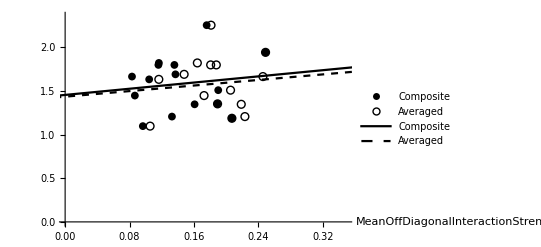

Composite P Value: {0.63088}       Averaged P Value: {0.711228}

Composite Correlation: 0.13522     Averaged Correlation: 0.104381

Composite R-Squared: 0.0182845      Averaged R-Squared: 0.0108953

```mathematica
lmRSquaredListFunction2[realHPCV,MeanOffDiagonalInteractionStrength,True](* no algae *)
```

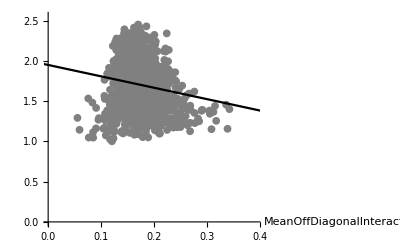

Composite P Value: {2.19771×10^-7}

Composite Correlation: -0.16297

Composite R-Squared: 0.0265591

```mathematica
lmRSquaredListFunctionGen[genPCV,MeanOffDiagonalInteractionStrength,True]
```

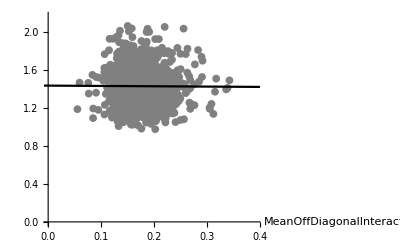

Composite P Value: {0.844713}

Composite Correlation: -0.0062016

Composite R-Squared: 0.0000384599

```mathematica
lmRSquaredListFunctionGen[genPCVrange,MeanOffDiagonalInteractionStrength,True]
```

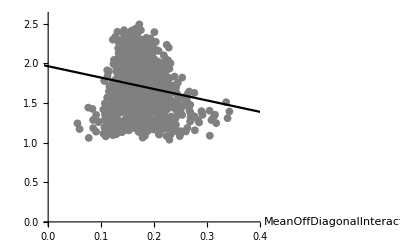

Composite P Value: {1.35559×10^-7}

Composite Correlation: -0.165742

Composite R-Squared: 0.0274704

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,MeanOffDiagonalInteractionStrength,True](* with covariates *)
```

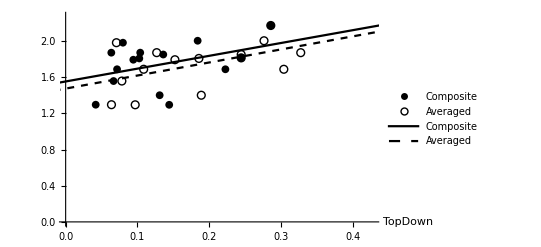

Composite P Value: {0.138341}       Averaged P Value: {0.0497639}

Composite Correlation: 0.401163     Averaged Correlation: 0.51443

Composite R-Squared: 0.160932      Averaged R-Squared: 0.264639

```mathematica
lmRSquaredListFunction2[realPCV,TopDown,True]
```

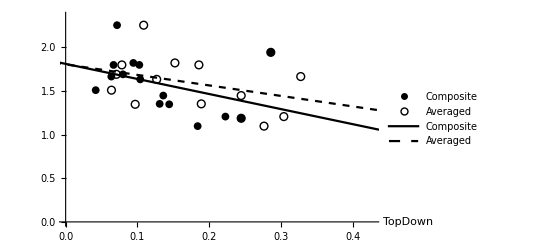

Composite P Value: {0.145705}       Averaged P Value: {0.206111}

Composite Correlation: -0.394433     Averaged Correlation: -0.346275

Composite R-Squared: 0.155577      Averaged R-Squared: 0.119906

```mathematica
lmRSquaredListFunction2[realHPCV,TopDown,True](* no algae *)
```

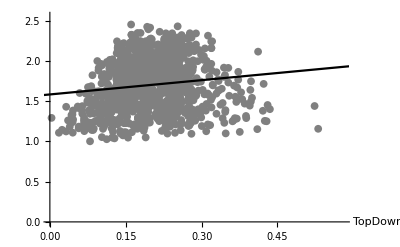

Composite P Value: {0.000021323}

Composite Correlation: 0.133976

Composite R-Squared: 0.0179495

```mathematica
lmRSquaredListFunctionGen[genPCV,TopDown,True]
```

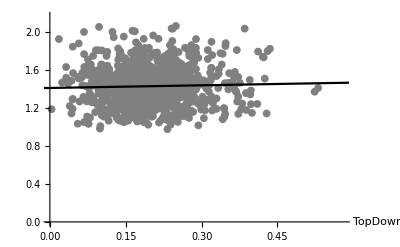

Composite P Value: {0.289072}

Composite Correlation: 0.0335577

Composite R-Squared: 0.00112612

```mathematica
lmRSquaredListFunctionGen[genPCVrange,TopDown,True]
```

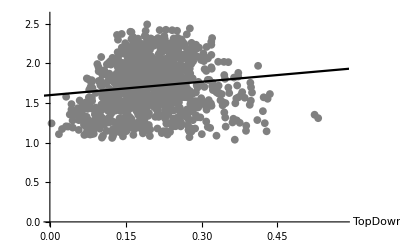

Composite P Value: {0.0000517299}

Composite Correlation: 0.127634

Composite R-Squared: 0.0162905

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,TopDown,True](* with covariates *)
```

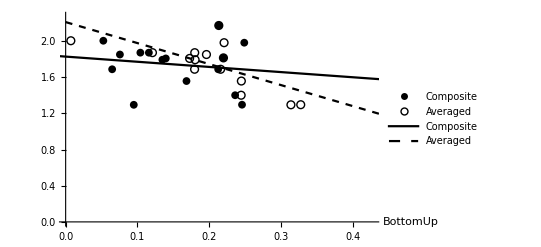

Composite P Value: {0.581239}       Averaged P Value: {0.00505083}

Composite Correlation: -0.154997     Averaged Correlation: -0.682538

Composite R-Squared: 0.0240242      Averaged R-Squared: 0.465858

```mathematica
lmRSquaredListFunction2[realPCV,BottomUp,True]
```

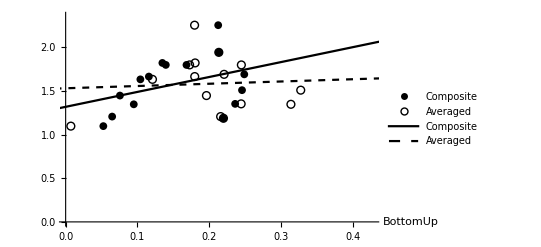

Composite P Value: {0.169093}       Averaged P Value: {0.827812}

Composite Correlation: 0.374462     Averaged Correlation: 0.0614376

Composite R-Squared: 0.140222      Averaged R-Squared: 0.00377458

```mathematica
lmRSquaredListFunction2[realHPCV,BottomUp,True](* no algae *)
```

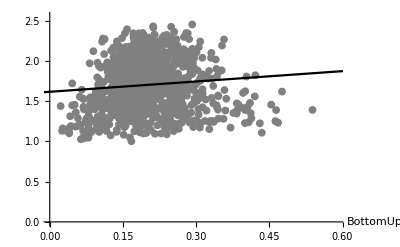

Composite P Value: {0.00229005}

Composite Correlation: 0.0963388

Composite R-Squared: 0.00928116

```mathematica
lmRSquaredListFunctionGen[genPCV,BottomUp,True]
```

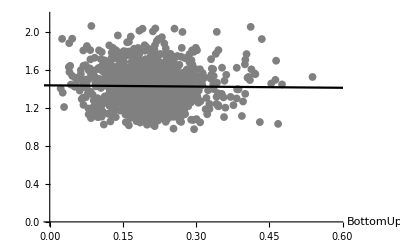

Composite P Value: {0.633041}

Composite Correlation: -0.0151164

Composite R-Squared: 0.000228505

```mathematica
lmRSquaredListFunctionGen[genPCVrange,BottomUp,True]
```

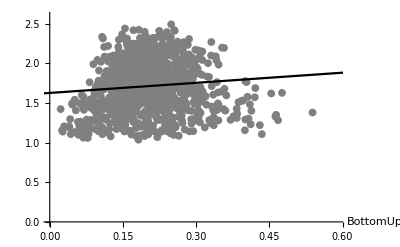

Composite P Value: {0.0023672}

Composite Correlation: 0.0960254

Composite R-Squared: 0.00922088

```mathematica
lmRSquaredListFunctionGen[genPCVwithC,BottomUp,True](* with covariates *)
```

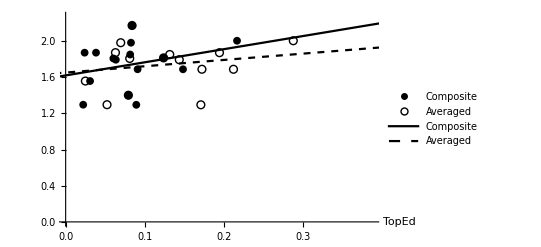

Composite P Value: {0.295689}       Averaged P Value: {0.487564}

Composite Correlation: 0.289272     Averaged Correlation: 0.194381

Composite R-Squared: 0.0836785      Averaged R-Squared: 0.0377838

```mathematica
lmRSquaredListFunction2[realPCV,TopEd,True]
```

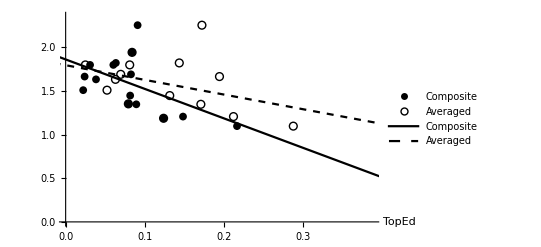

Composite P Value: {0.0363525}       Averaged P Value: {0.165167}

Composite Correlation: -0.543267     Averaged Correlation: -0.37768

Composite R-Squared: 0.295139      Averaged R-Squared: 0.142642

```mathematica
lmRSquaredListFunction2[realHPCV,TopEd,True]
```

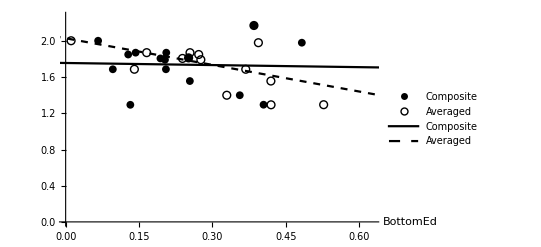

Composite P Value: {0.896852}       Averaged P Value: {0.0584761}

Composite Correlation: -0.0366405     Averaged Correlation: -0.498666

Composite R-Squared: 0.00134253      Averaged R-Squared: 0.248668

```mathematica
lmRSquaredListFunction2[realPCV,BottomEd,True]
```

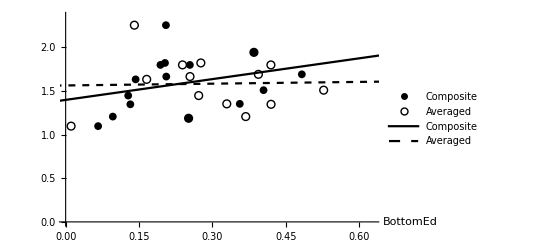

Composite P Value: {0.267595}       Averaged P Value: {0.922007}

Composite Correlation: 0.305849     Averaged Correlation: 0.0276756

Composite R-Squared: 0.0935437      Averaged R-Squared: 0.000765938

```mathematica
lmRSquaredListFunction2[realHPCV,BottomEd,True]
```

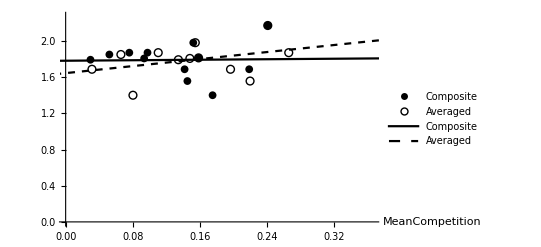

Composite P Value: {0.94466}       Averaged P Value: {0.258996}

Composite Correlation: 0.0225024     Averaged Correlation: 0.353953

Composite R-Squared: 0.000506359      Averaged R-Squared: 0.125283

```mathematica
lmRSquaredListFunction2[realPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),MeanCompetition,True,realPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),{19,20,22,24,25,26,27,28,29,30,31,32}]
```

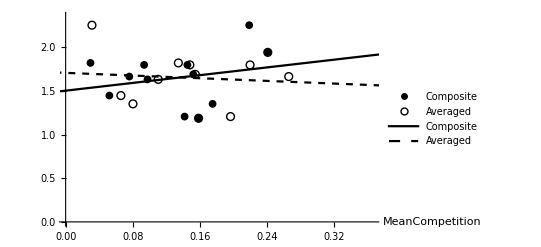

Composite P Value: {0.474501}       Averaged P Value: {0.784733}

Composite Correlation: 0.228765     Averaged Correlation: -0.0883878

Composite R-Squared: 0.0523336      Averaged R-Squared: 0.0078124

```mathematica
lmRSquaredListFunction2[realHPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),MeanCompetition,True,realHPCV[[#]]&/@({19,20,22,24,25,26,27,28,29,30,31,32}-17),{19,20,22,24,25,26,27,28,29,30,31,32}](* no algae *)
```

## 3. Interaction Strength vs. Theoretical

### Asymptotic Resilience

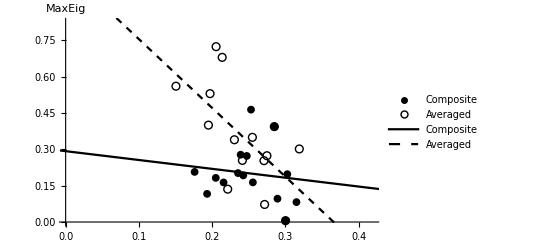

Composite P Value: {0.641241}       Averaged P Value: {0.0119034}

Composite Correlation: -0.131169     Averaged Correlation: -0.629568

Composite R-Squared: 0.0172053      Averaged R-Squared: 0.396356

```mathematica
lmRSquaredFunctions2[MaxEig,MeanInteractionStrength]
```

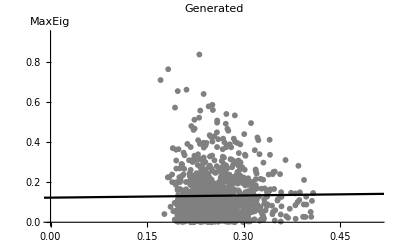

Composite P Value: {0.684449}

Composite Correlation: 0.0128671

Composite R-Squared: 0.000165561

```mathematica
lmRSquaredFunctionsGen[MaxEig,MeanInteractionStrength]
```

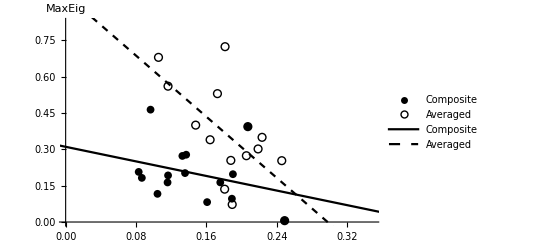

Composite P Value: {0.255869}       Averaged P Value: {0.0108233}

Composite Correlation: -0.313077     Averaged Correlation: -0.635944

Composite R-Squared: 0.0980174      Averaged R-Squared: 0.404424

```mathematica
lmRSquaredFunctions2[MaxEig,MeanOffDiagonalInteractionStrength]
```

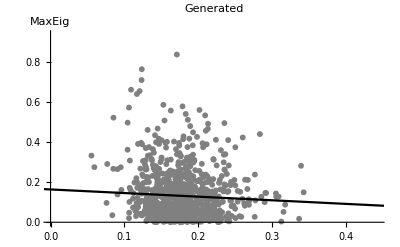

Composite P Value: {0.0744481}

Composite Correlation: -0.0564359

Composite R-Squared: 0.00318501

```mathematica
lmRSquaredFunctionsGen[MaxEig,MeanOffDiagonalInteractionStrength]
```

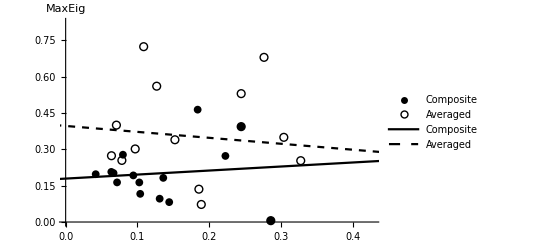

Composite P Value: {0.713951}       Averaged P Value: {0.7001}

Composite Correlation: 0.103357     Averaged Correlation: -0.108579

Composite R-Squared: 0.0106826      Averaged R-Squared: 0.0117894

```mathematica
lmRSquaredFunctions2[MaxEig,TopDown]
```

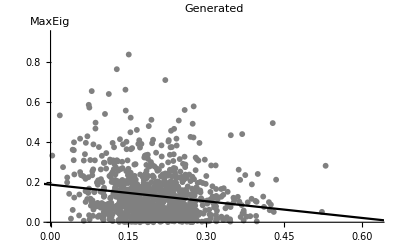

Composite P Value: {5.83281×10^-8}

Composite Correlation: -0.170474

Composite R-Squared: 0.0290612

```mathematica
lmRSquaredFunctionsGen[MaxEig,TopDown]
```

```mathematica
lmRSquaredFunctions2[MaxEig,BottomUp]
```

-Graphics-

Composite P Value: {0.478546}       Averaged P Value: {0.0433824}

Composite Correlation: -0.198348     Averaged Correlation: -0.527321

Composite R-Squared: 0.0393419      Averaged R-Squared: 0.278067

```mathematica
lmRSquaredFunctionsGen[MaxEig,BottomUp]
```

-Graphics-

Composite P Value: {0.00275221}

Composite Correlation: -0.0945889

Composite R-Squared: 0.00894706

```mathematica
lmRSquaredFunctions2[MaxEig,TopEd]
```

-Graphics-

Composite P Value: {0.0148219}       Averaged P Value: {0.0717249}

Composite Correlation: 0.614344     Averaged Correlation: 0.477694

Composite R-Squared: 0.377418      Averaged R-Squared: 0.228191

```mathematica
lmRSquaredFunctionsGen[MaxEig,TopEd]
```

-Graphics-

Composite P Value: {1.53339×10^-6}

Composite Correlation: -0.151319

Composite R-Squared: 0.0228973

```mathematica
lmRSquaredFunctions2[MaxEig,BottomEd]
```

-Graphics-

Composite P Value: {0.371624}       Averaged P Value: {0.0109323}

Composite Correlation: -0.248599     Averaged Correlation: -0.635278

Composite R-Squared: 0.0618017      Averaged R-Squared: 0.403578

```mathematica
lmRSquaredFunctionsGen[MaxEig,BottomEd]
```

-Graphics-

Composite P Value: {0.0404481}

Composite Correlation: -0.0648125

Composite R-Squared: 0.00420066

```mathematica
lmRSquaredFunctions2[MaxEig,TopIned]
```

-Graphics-

Composite P Value: {0.626959}       Averaged P Value: {0.199756}

Composite Correlation: -0.13676     Averaged Correlation: -0.350866

Composite R-Squared: 0.0187032      Averaged R-Squared: 0.123107

```mathematica
lmRSquaredFunctionsGen[MaxEig,TopIned]
```

-Graphics-

Composite P Value: {0.00273695}

Composite Correlation: -0.0946423

Composite R-Squared: 0.00895716

```mathematica
lmRSquaredFunctions2[MaxEig,BottomIned]
```

-Graphics-

Composite P Value: {0.864465}       Averaged P Value: {0.850084}

Composite Correlation: 0.048232     Averaged Correlation: 0.0534006

Composite R-Squared: 0.00232632      Averaged R-Squared: 0.00285162

```mathematica
lmRSquaredFunctionsGen[MaxEig,BottomIned]
```

-Graphics-

Composite P Value: {0.0242371}

Composite Correlation: -0.0712557

Composite R-Squared: 0.00507738

```mathematica
lmRSquaredFunctions2[MaxEig,MeanCompetition,{19,20,22,24,25,26,27,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.49037}       Averaged P Value: {0.0453895}

Composite Correlation: -0.220831     Averaged Correlation: -0.5857

Composite R-Squared: 0.0487662      Averaged R-Squared: 0.343045

```mathematica
lmRSquaredFunctionsGen[MaxEig,MeanCompetition,genbL]
```

-Graphics-

Composite P Value: {0.111547}

Composite Correlation: -0.0503517

Composite R-Squared: 0.00253529

### Initial Resilience

```mathematica
lmRSquaredFunctions2[Reactivity,MeanInteractionStrength]
```

-Graphics-

Composite P Value: {0.137077}       Averaged P Value: {0.0371287}

Composite Correlation: -0.402343     Averaged Correlation: -0.541399

Composite R-Squared: 0.16188      Averaged R-Squared: 0.293113

```mathematica
lmRSquaredFunctionsGen[Reactivity,MeanInteractionStrength]
```

-Graphics-

Composite P Value: {0.0259501}

Composite Correlation: 0.0704232

Composite R-Squared: 0.00495943

```mathematica
lmRSquaredFunctions2[Reactivity,MeanOffDiagonalInteractionStrength]
```

-Graphics-

Composite P Value: {0.0017284}       Averaged P Value: {0.000679288}

Composite Correlation: -0.736793     Averaged Correlation: -0.775575

Composite R-Squared: 0.542863      Averaged R-Squared: 0.601517

```mathematica
lmRSquaredFunctionsGen[Reactivity,MeanOffDiagonalInteractionStrength]
```

-Graphics-

Composite P Value: {4.68383×10^-8}

Composite Correlation: -0.171683

Composite R-Squared: 0.0294751

```mathematica
lmRSquaredFunctions2[Reactivity,TopDown]
```

-Graphics-

Composite P Value: {0.410642}       Averaged P Value: {0.372812}

Composite Correlation: -0.229489     Averaged Correlation: -0.248002

Composite R-Squared: 0.052665      Averaged R-Squared: 0.0615049

```mathematica
lmRSquaredFunctionsGen[Reactivity,TopDown]
```

-Graphics-

Composite P Value: {1.91063×10^-17}

Composite Correlation: -0.264302

Composite R-Squared: 0.0698557

```mathematica
lmRSquaredFunctions2[Reactivity,BottomUp]
```

-Graphics-

Composite P Value: {0.0245334}       Averaged P Value: {0.132652}

Composite Correlation: -0.576306     Averaged Correlation: -0.40653

Composite R-Squared: 0.332129      Averaged R-Squared: 0.165267

```mathematica
lmRSquaredFunctionsGen[Reactivity,BottomUp]
```

-Graphics-

Composite P Value: {1.65147×10^-18}

Composite Correlation: -0.272676

Composite R-Squared: 0.0743519

```mathematica
lmRSquaredFunctions2[Reactivity,TopEd]
```

-Graphics-

Composite P Value: {0.122738}       Averaged P Value: {0.20073}

Composite Correlation: 0.41627     Averaged Correlation: 0.350156

Composite R-Squared: 0.173281      Averaged R-Squared: 0.12261

```mathematica
lmRSquaredFunctionsGen[Reactivity,TopEd]
```

-Graphics-

Composite P Value: {1.2215×10^-11}

Composite Correlation: -0.212149

Composite R-Squared: 0.0450072

```mathematica
lmRSquaredFunctions2[Reactivity,BottomEd]
```

-Graphics-

Composite P Value: {0.0218827}       Averaged P Value: {0.0895394}

Composite Correlation: -0.585336     Averaged Correlation: -0.453504

Composite R-Squared: 0.342618      Averaged R-Squared: 0.205666

```mathematica
lmRSquaredFunctionsGen[Reactivity,BottomEd]
```

-Graphics-

Composite P Value: {1.17933×10^-11}

Composite Correlation: -0.212304

Composite R-Squared: 0.0450731

```mathematica
lmRSquaredFunctions2[Reactivity,TopIned]
```

-Graphics-

Composite P Value: {0.0878027}       Averaged P Value: {0.0863842}

Composite Correlation: -0.455703     Averaged Correlation: -0.457521

Composite R-Squared: 0.207665      Averaged R-Squared: 0.209326

```mathematica
lmRSquaredFunctionsGen[Reactivity,TopIned]
```

-Graphics-

Composite P Value: {7.36834×10^-8}

Composite Correlation: -0.169176

Composite R-Squared: 0.0286204

```mathematica
lmRSquaredFunctions2[Reactivity,BottomIned]
```

-Graphics-

Composite P Value: {0.609633}       Averaged P Value: {0.904795}

Composite Correlation: -0.143608     Averaged Correlation: -0.0338064

Composite R-Squared: 0.0206231      Averaged R-Squared: 0.00114287

```mathematica
lmRSquaredFunctionsGen[Reactivity,BottomIned]
```

-Graphics-

Composite P Value: {7.88291×10^-9}

Composite Correlation: -0.181207

Composite R-Squared: 0.032836

```mathematica
lmRSquaredFunctions2[Reactivity,MeanCompetition,{19,20,22,24,25,26,27,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.0302025}       Averaged P Value: {0.0112309}

Composite Correlation: -0.623751     Averaged Correlation: -0.700159

Composite R-Squared: 0.389065      Averaged R-Squared: 0.490222

```mathematica
lmRSquaredFunctionsGen[Reactivity,MeanCompetition,genbL]
```

-Graphics-

Composite P Value: {0.0488898}

Composite Correlation: -0.0623001

Composite R-Squared: 0.0038813

### Intrinsic Stochastic Invariability

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,MeanInteractionStrength]
```

-Graphics-

Composite P Value: {0.232735}       Averaged P Value: {0.0328897}

Composite Correlation: -0.327957     Averaged Correlation: -0.551985

Composite R-Squared: 0.107556      Averaged R-Squared: 0.304687

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,MeanOffDiagonalInteractionStrength]
```

-Graphics-

Composite P Value: {0.041243}       Averaged P Value: {0.0391255}

Composite Correlation: -0.531956     Averaged Correlation: -0.536724

Composite R-Squared: 0.282977      Averaged R-Squared: 0.288073

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,TopDown]
```

-Graphics-

Composite P Value: {0.950976}       Averaged P Value: {0.832307}

Composite Correlation: 0.0173814     Averaged Correlation: -0.0598123

Composite R-Squared: 0.000302112      Averaged R-Squared: 0.00357751

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,BottomUp]
```

-Graphics-

Composite P Value: {0.164349}       Averaged P Value: {0.0924636}

Composite Correlation: -0.378358     Averaged Correlation: -0.449869

Composite R-Squared: 0.143155      Averaged R-Squared: 0.202383

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,TopEd]
```

-Graphics-

Composite P Value: {0.0190414}       Averaged P Value: {0.0212399}

Composite Correlation: 0.595994     Averaged Correlation: 0.58765

Composite R-Squared: 0.355209      Averaged R-Squared: 0.345332

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,TopEd]
```

-Graphics-

Composite P Value: {1.18367×10^-8}

Composite Correlation: -0.179079

Composite R-Squared: 0.0320695

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,BottomEd]
```

-Graphics-

Composite P Value: {0.177561}       Averaged P Value: {0.0268568}

Composite Correlation: -0.367684     Averaged Correlation: -0.568983

Composite R-Squared: 0.135192      Averaged R-Squared: 0.323742

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,BottomEd]
```

-Graphics-

Composite P Value: {0.000167026}

Composite Correlation: -0.118764

Composite R-Squared: 0.0141049

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,TopIned]
```

-Graphics-

Composite P Value: {0.403027}       Averaged P Value: {0.209463}

Composite Correlation: -0.23314     Averaged Correlation: -0.343889

Composite R-Squared: 0.0543542      Averaged R-Squared: 0.11826

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,TopIned]
```

-Graphics-

Composite P Value: {0.000164567}

Composite Correlation: -0.11888

Composite R-Squared: 0.0141325

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,BottomIned]
```

-Graphics-

Composite P Value: {0.647662}       Averaged P Value: {0.719107}

Composite Correlation: -0.12867     Averaged Correlation: 0.101421

Composite R-Squared: 0.016556      Averaged R-Squared: 0.0102861

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,BottomIned]
```

-Graphics-

Composite P Value: {0.000492852}

Composite Correlation: -0.109996

Composite R-Squared: 0.0120992

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,MeanCompetition,{19,20,22,24,25,26,27,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.158595}       Averaged P Value: {0.0469126}

Composite Correlation: -0.434045     Averaged Correlation: -0.582416

Composite R-Squared: 0.188395      Averaged R-Squared: 0.339208

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,MeanCompetition,genbL]
```

-Graphics-

Composite P Value: {0.142425}

Composite Correlation: -0.046418

Composite R-Squared: 0.00215463

## 4. Interaction Strength vs. Richness/Composition

### Richness (Number of Species, Length)

```mathematica
lmRSquaredFunctions2[MeanInteractionStrength,Length]
```

-Graphics-

Composite P Value: {0.00139243}       Averaged P Value: {0.209696}

Composite Correlation: -0.746397     Averaged Correlation: -0.343724

Composite R-Squared: 0.557108      Averaged R-Squared: 0.118147

```mathematica
lmRSquaredFunctionsGen[MeanInteractionStrength,Length]
```

-Graphics-

Composite P Value: {3.82513×10^-138}

Composite Correlation: -0.682692

Composite R-Squared: 0.466069

```mathematica
lmRSquaredFunctions2[MeanOffDiagonalInteractionStrength,Length]
```

-Graphics-

Composite P Value: {0.245456}       Averaged P Value: {0.742567}

Composite Correlation: -0.319668     Averaged Correlation: 0.0926633

Composite R-Squared: 0.102188      Averaged R-Squared: 0.00858649

```mathematica
lmRSquaredFunctionsGen[MeanOffDiagonalInteractionStrength,Length]
```

-Graphics-

Composite P Value: {7.0911×10^-22}

Composite Correlation: -0.297436

Composite R-Squared: 0.0884679

```mathematica
lmRSquaredFunctions2[TopDown,Length]
```

-Graphics-

Composite P Value: {0.717199}       Averaged P Value: {0.315575}

Composite Correlation: -0.102137     Averaged Correlation: 0.278094

Composite R-Squared: 0.0104319      Averaged R-Squared: 0.0773361

```mathematica
lmRSquaredFunctionsGen[TopDown,Length]
```

-Graphics-

Composite P Value: {0.130571}

Composite Correlation: 0.0478415

Composite R-Squared: 0.00228881

```mathematica
lmRSquaredFunctions2[BottomUp,Length]
```

-Graphics-

Composite P Value: {0.622822}       Averaged P Value: {0.419057}

Composite Correlation: -0.138388     Averaged Correlation: -0.225494

Composite R-Squared: 0.0191512      Averaged R-Squared: 0.0508477

```mathematica
lmRSquaredFunctions2[TopEd,Length]
```

-Graphics-

Composite P Value: {0.0506695}       Averaged P Value: {0.257338}

Composite Correlation: -0.512702     Averaged Correlation: -0.312161

Composite R-Squared: 0.262863      Averaged R-Squared: 0.0974443

```mathematica
lmRSquaredFunctionsGen[TopEd,Length]
```

-Graphics-

Composite P Value: {0.189996}

Composite Correlation: 0.0414786

Composite R-Squared: 0.00172048

```mathematica
lmRSquaredFunctions2[BottomEd,Length]
```

-Graphics-

Composite P Value: {0.809271}       Averaged P Value: {0.565262}

Composite Correlation: -0.0681618     Averaged Correlation: -0.161507

Composite R-Squared: 0.00464603      Averaged R-Squared: 0.0260844

```mathematica
lmRSquaredFunctionsGen[BottomEd,Length]
```

-Graphics-

Composite P Value: {0.251897}

Composite Correlation: 0.0362654

Composite R-Squared: 0.00131518

```mathematica
lmRSquaredFunctions2[TopIned,Length]
```

-Graphics-

Composite P Value: {0.736593}       Averaged P Value: {0.0731002}

Composite Correlation: 0.0948856     Averaged Correlation: 0.475682

Composite R-Squared: 0.00900327      Averaged R-Squared: 0.226274

```mathematica
lmRSquaredFunctionsGen[TopIned,Length]
```

-Graphics-

Composite P Value: {0.384197}

Composite Correlation: 0.027547

Composite R-Squared: 0.000758839

```mathematica
lmRSquaredFunctions2[BottomIned,Length]
```

-Graphics-

Composite P Value: {0.510492}       Averaged P Value: {0.463686}

Composite Correlation: -0.184447     Averaged Correlation: -0.204964

Composite R-Squared: 0.0340209      Averaged R-Squared: 0.0420103

```mathematica
lmRSquaredFunctionsGen[BottomIned,Length]
```

-Graphics-

Composite P Value: {0.933987}

Composite Correlation: 0.00262256

Composite R-Squared: 6.87784×10^-6

### No Daphnia vs. Contains Daphnia

```mathematica
lmRSquaredListFunction2[containsDap,MeanInteractionStrength,False]
```

-Graphics-

Composite P Value: {0.211527}       Averaged P Value: {0.454509}

Composite Correlation: -0.342432     Averaged Correlation: -0.209102

Composite R-Squared: 0.11726      Averaged R-Squared: 0.0437237

```mathematica
lmRSquaredListFunction2[containsDap,MeanOffDiagonalInteractionStrength,False]
```

-Graphics-

Composite P Value: {0.499993}       Averaged P Value: {0.784398}

Composite Correlation: -0.18897     Averaged Correlation: -0.0772364

Composite R-Squared: 0.0357096      Averaged R-Squared: 0.00596547

```mathematica
lmRSquaredListFunction2[containsDap,TopDown,False]
```

-Graphics-

Composite P Value: {0.0518279}       Averaged P Value: {0.0134164}

Composite Correlation: 0.510523     Averaged Correlation: 0.621354

Composite R-Squared: 0.260634      Averaged R-Squared: 0.38608

```mathematica
lmRSquaredListFunction2[containsDap,BottomUp,False]
```

-Graphics-

Composite P Value: {0.294944}       Averaged P Value: {0.0918058}

Composite Correlation: -0.289699     Averaged Correlation: -0.45068

Composite R-Squared: 0.0839256      Averaged R-Squared: 0.203112

```mathematica
lmRSquaredListFunction2[containsDap,TopEd,False]
```

-Graphics-

Composite P Value: {0.163835}       Averaged P Value: {0.26799}

Composite Correlation: 0.378784     Averaged Correlation: 0.305609

Composite R-Squared: 0.143477      Averaged R-Squared: 0.0933969

```mathematica
lmRSquaredListFunction2[containsDap,BottomEd,False]
```

-Graphics-

Composite P Value: {0.653797}       Averaged P Value: {0.293931}

Composite Correlation: -0.126291     Averaged Correlation: -0.290281

Composite R-Squared: 0.0159495      Averaged R-Squared: 0.0842633

```mathematica
lmRSquaredListFunction2[containsDap,TopIned,False]
```

-Graphics-

Composite P Value: {0.0866176}       Averaged P Value: {0.0187182}

Composite Correlation: 0.457221     Averaged Correlation: 0.597282

Composite R-Squared: 0.209051      Averaged R-Squared: 0.356746

```mathematica
lmRSquaredListFunction2[containsDap,BottomIned,False]
```

-Graphics-

Composite P Value: {0.118997}       Averaged P Value: {0.0722788}

Composite Correlation: -0.420086     Averaged Correlation: -0.47688

Composite R-Squared: 0.176473      Averaged R-Squared: 0.227415

## 5. Other Interaction Strengths vs. Theoretical

### Top Ratio between Edible and Inedible

```mathematica
lmRSquaredFunctions2[TopRatioEdIned,MaxEig]
```

-Graphics-

Composite P Value: {0.123449}       Averaged P Value: {0.415089}

Composite Correlation: 0.415554     Averaged Correlation: 0.227372

Composite R-Squared: 0.172685      Averaged R-Squared: 0.0516982

```mathematica
lmRSquaredFunctionsGen[TopRatioEdIned,MaxEig]
```

-Graphics-

Composite P Value: {0.841913}

Composite Correlation: -0.00631489

Composite R-Squared: 0.0000398778

```mathematica
lmRSquaredFunctions2[TopRatioEdIned,Reactivity]
```

-Graphics-

Composite P Value: {0.183809}       Averaged P Value: {0.472386}

Composite Correlation: 0.362819     Averaged Correlation: 0.201078

Composite R-Squared: 0.131637      Averaged R-Squared: 0.0404325

```mathematica
lmRSquaredFunctions2[TopRatioEdIned,IntrinsicStochasticInvariability]
```

-Graphics-

Composite P Value: {0.0916926}       Averaged P Value: {0.223464}

Composite Correlation: 0.45082     Averaged Correlation: 0.334178

Composite R-Squared: 0.203238      Averaged R-Squared: 0.111675

### Bottom Ratio between Edible and Inedible

```mathematica
lmRSquaredFunctions2[BotRatioEdIned,MaxEig]
```

-Graphics-

Composite P Value: {0.856383}       Averaged P Value: {0.146124}

Composite Correlation: 0.0511348     Averaged Correlation: -0.394057

Composite R-Squared: 0.00261477      Averaged R-Squared: 0.155281

```mathematica
lmRSquaredFunctions2[BotRatioEdIned,Reactivity]
```

-Graphics-

Composite P Value: {0.753302}       Averaged P Value: {0.250846}

Composite Correlation: -0.0886823     Averaged Correlation: -0.316236

Composite R-Squared: 0.00786455      Averaged R-Squared: 0.100005

```mathematica
lmRSquaredFunctions2[BotRatioEdIned,IntrinsicStochasticInvariability]
```

-Graphics-

Composite P Value: {0.775266}       Averaged P Value: {0.126882}

Composite Correlation: 0.0805856     Averaged Correlation: -0.412136

Composite R-Squared: 0.00649404      Averaged R-Squared: 0.169856

### Effect of Daphnia on Edible Algae

```mathematica
lmRSquaredListFunction2[daplistTe,MaxEig,True,daplistTeavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.112127}       Averaged P Value: {0.817665}

Composite Correlation: -0.60488     Averaged Correlation: -0.0978686

Composite R-Squared: 0.365879      Averaged R-Squared: 0.00957826

```mathematica
lmRSquaredListFunction2[daplistTe,Reactivity,True,daplistTeavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.815404}       Averaged P Value: {0.995938}

Composite Correlation: -0.0990978     Averaged Correlation: 0.00216635

Composite R-Squared: 0.00982038      Averaged R-Squared:           -6
4.69309 10

```mathematica
lmRSquaredListFunction2[daplistTe,IntrinsicStochasticInvariability,True,daplistTeavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.437588}       Averaged P Value: {0.66559}

Composite Correlation: -0.3214     Averaged Correlation: -0.182354

Composite R-Squared: 0.103298      Averaged R-Squared: 0.0332531

### Effect of Daphnia on Inedible Algae

```mathematica
lmRSquaredListFunction2[daplistTi,MaxEig,True,daplistTiavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.90632}       Averaged P Value: {0.796854}

Composite Correlation: -0.0500463     Averaged Correlation: -0.10921

Composite R-Squared: 0.00250463      Averaged R-Squared: 0.0119268

```mathematica
lmRSquaredListFunction2[daplistTi,Reactivity,True,daplistTiavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.903644}       Averaged P Value: {0.859135}

Composite Correlation: -0.0514805     Averaged Correlation: -0.0754133

Composite R-Squared: 0.00265024      Averaged R-Squared: 0.00568716

```mathematica
lmRSquaredListFunction2[daplistTi,IntrinsicStochasticInvariability,True,daplistTiavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.798922}       Averaged P Value: {0.803796}

Composite Correlation: 0.10808     Averaged Correlation: -0.105421

Composite R-Squared: 0.0116813      Averaged R-Squared: 0.0111135

### Effect of Edible Algae on Daphnia

```mathematica
lmRSquaredListFunction2[daplistBe,MaxEig,True,daplistBeavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.720076}       Averaged P Value: {0.411583}

Composite Correlation: -0.151599     Averaged Correlation: 0.338871

Composite R-Squared: 0.0229824      Averaged R-Squared: 0.114834

```mathematica
lmRSquaredListFunction2[daplistBe,Reactivity,True,daplistBeavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.950573}       Averaged P Value: {0.872708}

Composite Correlation: 0.0263732     Averaged Correlation: 0.0680995

Composite R-Squared: 0.000695547      Averaged R-Squared: 0.00463755

```mathematica
lmRSquaredListFunction2[daplistBe,IntrinsicStochasticInvariability,True,daplistBeavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.816549}       Averaged P Value: {0.62768}

Composite Correlation: -0.0984755     Averaged Correlation: 0.204174

Composite R-Squared: 0.00969743      Averaged R-Squared: 0.041687

### Effect of Inedible Algae on Daphnia

```mathematica
lmRSquaredListFunction2[daplistBi,MaxEig,True,daplistBiavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.279304}       Averaged P Value: {0.89062}

Composite Correlation: 0.436724     Averaged Correlation: -0.0584692

Composite R-Squared: 0.190728      Averaged R-Squared: 0.00341865

```mathematica
lmRSquaredListFunction2[daplistBi,Reactivity,True,daplistBiavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.824955}       Averaged P Value: {0.738031}

Composite Correlation: 0.0939079     Averaged Correlation: 0.141598

Composite R-Squared: 0.00881869      Averaged R-Squared: 0.02005

```mathematica
lmRSquaredListFunction2[daplistBi,IntrinsicStochasticInvariability,True,daplistBiavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.602102}       Averaged P Value: {0.798169}

Composite Correlation: 0.219126     Averaged Correlation: -0.108491

Composite R-Squared: 0.048016      Averaged R-Squared: 0.0117704

### Ratio between Daphnia on Edible and Daphnia on Inedible

```mathematica
lmRSquaredListFunction2[daptopRatio,MaxEig,True,daptopRatioavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.629319}       Averaged P Value: {0.480457}

Composite Correlation: 0.203222     Averaged Correlation: -0.293511

Composite R-Squared: 0.0412993      Averaged R-Squared: 0.0861488

```mathematica
lmRSquaredListFunction2[daptopRatio,Reactivity,True,daptopRatioavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.689229}       Averaged P Value: {0.828352}

Composite Correlation: -0.168931     Averaged Correlation: -0.0920643

Composite R-Squared: 0.0285376      Averaged R-Squared: 0.00847583

```mathematica
lmRSquaredListFunction2[daptopRatio,IntrinsicStochasticInvariability,True,daptopRatioavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.813946}       Averaged P Value: {0.456414}

Composite Correlation: 0.0998911     Averaged Correlation: -0.309023

Composite R-Squared: 0.00997823      Averaged R-Squared: 0.0954949

### Ratio between Edible and Inedible on Daphnia

```mathematica
lmRSquaredListFunction2[dapbotRatio,MaxEig,True,dapbotRatioavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.81152}       Averaged P Value: {0.130435}

Composite Correlation: 0.101212     Averaged Correlation: -0.58163

Composite R-Squared: 0.0102438      Averaged R-Squared: 0.338293

```mathematica
lmRSquaredListFunction2[dapbotRatio,Reactivity,True,dapbotRatioavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.637888}       Averaged P Value: {0.048679}

Composite Correlation: -0.19826     Averaged Correlation: -0.709569

Composite R-Squared: 0.0393071      Averaged R-Squared: 0.503489

```mathematica
lmRSquaredListFunction2[dapbotRatio,IntrinsicStochasticInvariability,True,dapbotRatioavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.864166}       Averaged P Value: {0.0897423}

Composite Correlation: -0.0727007     Averaged Correlation: -0.636466

Composite R-Squared: 0.00528538      Averaged R-Squared: 0.405089

### Ratio between Cerodaphnia on Edible and Cerodaphnia on Inedible

```mathematica
lmRSquaredListFunction2[certopRatio,MaxEig,True,certopRatioavg,{18,19,20,24,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.605053}       Averaged P Value: {0.038415}

Composite Correlation: -0.200461     Averaged Correlation: 0.69317

Composite R-Squared: 0.0401848      Averaged R-Squared: 0.480485

```mathematica
lmRSquaredListFunction2[certopRatio,Reactivity,True,certopRatioavg,{18,19,20,24,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.985932}       Averaged P Value: {0.504424}

Composite Correlation: 0.00690584     Averaged Correlation: 0.256992

Composite R-Squared: 0.0000476907      Averaged R-Squared: 0.0660451

```mathematica
lmRSquaredListFunction2[certopRatio,IntrinsicStochasticInvariability,True,certopRatioavg,{18,19,20,24,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.663276}       Averaged P Value: {0.0396478}

Composite Correlation: -0.169279     Averaged Correlation: 0.690091

Composite R-Squared: 0.0286555      Averaged R-Squared: 0.476226

### Ratio between Edible and Inedible on Cerodaphnia

```mathematica
lmRSquaredListFunction2[cerbotRatio,MaxEig,True,cerbotRatioavg,{18,19,20,24,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.108376}       Averaged P Value: {0.956822}

Composite Correlation: -0.570915     Averaged Correlation: 0.0212028

Composite R-Squared: 0.325944      Averaged R-Squared: 0.000449561

```mathematica
lmRSquaredListFunction2[cerbotRatio,Reactivity,True,cerbotRatioavg,{18,19,20,24,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.68405}       Averaged P Value: {0.209794}

Composite Correlation: -0.158364     Averaged Correlation: -0.462692

Composite R-Squared: 0.0250791      Averaged R-Squared: 0.214084

```mathematica
lmRSquaredListFunction2[cerbotRatio,IntrinsicStochasticInvariability,True,cerbotRatioavg,{18,19,20,24,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.600281}       Averaged P Value: {0.871013}

Composite Correlation: -0.20306     Averaged Correlation: -0.0635299

Composite R-Squared: 0.0412334      Averaged R-Squared: 0.00403604

### Ratio Between Edible Top and Bottom

```mathematica
lmRSquaredFunctions2[MaxEig,TopBottomRatio]
```

-Graphics-

Composite P Value: {0.106116}       Averaged P Value: {0.106454}

Composite Correlation: 0.433893     Averaged Correlation: 0.433517

Composite R-Squared: 0.188264      Averaged R-Squared: 0.187937

```mathematica
lmRSquaredFunctionsGen[MaxEig,TopBottomRatio]
```

-Graphics-

Composite P Value: {0.0525867}

Composite Correlation: 0.0613134

Composite R-Squared: 0.00375934

```mathematica
lmRSquaredFunctions2[Reactivity,TopBottomRatio]
```

-Graphics-

Composite P Value: {0.112024}       Averaged P Value: {0.0834561}

Composite Correlation: 0.427425     Averaged Correlation: 0.461344

Composite R-Squared: 0.182692      Averaged R-Squared: 0.212838

```mathematica
lmRSquaredFunctionsGen[Reactivity,TopBottomRatio]
```

-Graphics-

Composite P Value: {0.00290392}

Composite Correlation: 0.0940729

Composite R-Squared: 0.0088497

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,TopBottomRatio]
```

-Graphics-

Composite P Value: {0.0561112}       Averaged P Value: {0.161716}

Composite Correlation: 0.502765     Averaged Correlation: 0.380552

Composite R-Squared: 0.252773      Averaged R-Squared: 0.144819

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,TopBottomRatio]
```

-Graphics-

Composite P Value: {0.0113207}

Composite Correlation: 0.0800607

Composite R-Squared: 0.00640971

### Ratio Between Mean Bottom and Mean Top

```mathematica
lmRSquaredFunctions2[MaxEig,BottomTopRatio]
```

-Graphics-

Composite P Value: {0.786196}       Averaged P Value: {0.596226}

Composite Correlation: -0.076578     Averaged Correlation: -0.148958

Composite R-Squared: 0.00586419      Averaged R-Squared: 0.0221886

```mathematica
lmRSquaredFunctionsGen[MaxEig,BottomTopRatio]
```

-Graphics-

Composite P Value: {0.0000413039}

Composite Correlation: 0.129273

Composite R-Squared: 0.0167114

```mathematica
lmRSquaredFunctions2[Reactivity,BottomTopRatio]
```

-Graphics-

Composite P Value: {0.464822}       Averaged P Value: {0.9028}

Composite Correlation: -0.204455     Averaged Correlation: -0.0345181

Composite R-Squared: 0.0418018      Averaged R-Squared: 0.0011915

```mathematica
lmRSquaredFunctionsGen[Reactivity,BottomTopRatio]
```

-Graphics-

Composite P Value: {0.0154051}

Composite Correlation: 0.0765961

Composite R-Squared: 0.00586696

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,BottomTopRatio]
```

-Graphics-

Composite P Value: {0.555105}       Averaged P Value: {0.618352}

Composite Correlation: -0.165685     Averaged Correlation: -0.140152

Composite R-Squared: 0.0274515      Averaged R-Squared: 0.0196426

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,BottomTopRatio]
```

-Graphics-

Composite P Value: {0.000399981}

Composite Correlation: 0.111737

Composite R-Squared: 0.0124851

### Effect of Daphnia on Itself

```mathematica
lmRSquaredListFunction2[dapselflist,MaxEig,True,dapselflistavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.855628}       Averaged P Value: {0.925445}

Composite Correlation: -0.0773061     Averaged Correlation: 0.0398049

Composite R-Squared: 0.00597623      Averaged R-Squared: 0.00158443

```mathematica
lmRSquaredListFunction2[dapselflist,Reactivity,True,dapselflistavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.311421}       Averaged P Value: {0.464523}

Composite Correlation: 0.411262     Averaged Correlation: 0.303755

Composite R-Squared: 0.169137      Averaged R-Squared: 0.0922672

```mathematica
lmRSquaredListFunction2[dapselflist,IntrinsicStochasticInvariability,True,dapselflistavg,{19,21,22,24,25,27,29,32}]
```

-Graphics-

Composite P Value: {0.609424}       Averaged P Value: {0.886245}

Composite Correlation: 0.214825     Averaged Correlation: -0.0608193

Composite R-Squared: 0.0461499      Averaged R-Squared: 0.00369899

## 6. Theoretical vs. Richness/Composition

### Richness (Number of Species, Length)

```mathematica
lmRSquaredFunctions2[MaxEig,Length]
```

-Graphics-

Composite P Value: {0.209047}       Averaged P Value: {0.56223}

Composite Correlation: -0.344184     Averaged Correlation: -0.162751

Composite R-Squared: 0.118463      Averaged R-Squared: 0.0264878

```mathematica
lmRSquaredFunctionsGen[MaxEig,Length]
```

-Graphics-

Composite P Value: {5.46971×10^-50}

Composite Correlation: -0.445788

Composite R-Squared: 0.198727

```mathematica
lmRSquaredFunctions2[Reactivity,Length]
```

-Graphics-

Composite P Value: {0.461428}       Averaged P Value: {0.0630767}

Composite Correlation: -0.205978     Averaged Correlation: -0.491026

Composite R-Squared: 0.0424271      Averaged R-Squared: 0.241107

```mathematica
lmRSquaredFunctionsGen[Reactivity,Length]
```

-Graphics-

Composite P Value: {6.4108×10^-126}

Composite Correlation: -0.659639

Composite R-Squared: 0.435124

```mathematica
lmRSquaredFunctions2[IntrinsicStochasticInvariability,Length]
```

-Graphics-

Composite P Value: {0.409376}       Averaged P Value: {0.375732}

Composite Correlation: -0.230093     Averaged Correlation: -0.246538

Composite R-Squared: 0.0529428      Averaged R-Squared: 0.0607809

```mathematica
lmRSquaredFunctionsGen[IntrinsicStochasticInvariability,Length]
```

-Graphics-

Composite P Value: {4.32265×10^-78}

Composite Correlation: -0.543965

Composite R-Squared: 0.295898

### No Daphnia vs. Contains Daphnia

```mathematica
lmRSquaredListFunction2[containsDap,MaxEig,False]
```

-Graphics-

Composite P Value: {0.177566}       Averaged P Value: {0.387081}

Composite Correlation: 0.36768     Averaged Correlation: 0.240906

Composite R-Squared: 0.135189      Averaged R-Squared: 0.0580355

```mathematica
lmRSquaredListFunction2[containsDap,Reactivity,False]
```

-Graphics-

Composite P Value: {0.524518}       Averaged P Value: {0.889111}

Composite Correlation: 0.178473     Averaged Correlation: 0.0394054

Composite R-Squared: 0.0318524      Averaged R-Squared: 0.00155278

```mathematica
lmRSquaredListFunction2[containsDap,IntrinsicStochasticInvariability,False]
```

-Graphics-

Composite P Value: {0.0934358}       Averaged P Value: {0.445945}

Composite Correlation: 0.448679     Averaged Correlation: 0.213001

Composite R-Squared: 0.201313      Averaged R-Squared: 0.0453694

## 7. Competition vs. Theoretical, Empirical, and Richness/Composition

```mathematica
(* If there is only one predator species, that composition is ignored *)
```

### Richness and Composition

```mathematica
lmRSquaredFunctions2[MeanCompetition,Length,{19,20,22,24,25,26,27,28,29,30,31,32}]
```

-Graphics-

Composite P Value: {0.311966}       Averaged P Value: {0.246591}

Composite Correlation: -0.319136     Averaged Correlation: 0.362688

Composite R-Squared: 0.101848      Averaged R-Squared: 0.131542

```mathematica
lmRSquaredFunctionsGen[MeanCompetition,Length,genbL]
```

-Graphics-

Composite P Value: {0.156509}

Composite Correlation: 0.0448402

Composite R-Squared: 0.00201064

```mathematica
lmRSquaredListFunction2[containsDap,MeanCompetition,False](* includes tanks with 0 competition *)
```

-Graphics-

Composite P Value: {0.637278}       Averaged P Value: {0.19297}

Composite Correlation: 0.132715     Averaged Correlation: 0.355874

Composite R-Squared: 0.0176134      Averaged R-Squared: 0.126647

## Graphics Grids

```mathematica
Grid[{{Rotate[Text[Style["CCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionx[realCCV,MaxEig,True,True,False,0,False,False],lmRSquaredListFunctionx[realCCV,Reactivity,True,False,False,0,False,False],lmRSquaredListFunctionx[realCCV,IntrinsicStochasticInvariability,True,False,False,0,False,False]},{Rotate[Text[Style["PCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionx[realPCV,MaxEig,True,True,False,0,False,False],lmRSquaredListFunctionx[realPCV,Reactivity,True,False,False,0,False,False],lmRSquaredListFunctionx[realPCV,IntrinsicStochasticInvariability,True,False,False,0,False,False]},{Rotate[Text[Style["WPCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionx[realWPCV,MaxEig,True,True,True,0,False,False],lmRSquaredListFunctionx[realWPCV,Reactivity,True,False,True,0,False,False],lmRSquaredListFunctionx[realWPCV,IntrinsicStochasticInvariability,True,False,True,0,False,False]},{Text[""],Text[Style["Asymptotic Resilience",FontFamily->"Arial"]],Text[Style["Initial Resilience",FontFamily->"Arial"]],Text[Style["Intrinsic Stochastic Invariability",FontFamily->"Arial"]]}}]
```

CCV | -Graphics- | -Graphics- | -Graphics-
PCV | -Graphics- | -Graphics- | -Graphics-
WPCV | -Graphics- | -Graphics- | -Graphics-
 | Asymptotic Resilience | Initial Resilience | Intrinsic Stochastic Invariability

```mathematica
Mean[{0.8250,0.5819,0.1282,0.3072,0.6422,0.3506,0.4420,0.5623,0.7787,0.8733,0.3598,0.7428,0.8136,0.3139,0.0687,0.1425,0.4600,0.1703}]
```

0.475722

```mathematica
Mean[{0.024,0.004,0.080,0.169,0.067,0.017,0.026,0.046,0.002,0.006,0.009,0.065,0.078,0.004,0.158,0.223,0.139,0.043}]
```

0.0644444

```mathematica
Max[{0.024,0.004,0.080,0.169,0.067,0.017,0.026,0.046,0.002,0.006,0.009,0.065,0.078,0.004,0.158,0.223,0.139,0.043}]
```

0.223

```mathematica
Grid[{
{Rotate[Text[Style["CCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionx[realCCV,MeanInteractionStrength,True,True,False,0,False,True],lmRSquaredListFunctionx[realCCV,MeanOffDiagonalInteractionStrength,True,False,False,1,False,True],lmRSquaredListFunctionx[realCCV,TopDown,True,False,False,2,False,True],
lmRSquaredListFunctionx[realCCV,BottomUp,True,False,False,0,False,True],
lmRSquaredListFunctionx[realCCV,TopEd,True,False,False,0,False,True],
lmRSquaredListFunctionx[realCCV,BottomEd,True,False,False,0,False,True],
lmRSquaredListFunctionx[realCCV,MeanCompetition,True,False,False,0,True,True]},

{Rotate[Text[Style["PCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionx[realPCV,MeanInteractionStrength,True,True,False,0,False,True],lmRSquaredListFunctionx[realPCV,MeanOffDiagonalInteractionStrength,True,False,False,0,False,True],
lmRSquaredListFunctionx[realPCV,TopDown,True,False,False,1,False,True],
lmRSquaredListFunctionx[realPCV,BottomUp,True,False,False,2,False,True],
lmRSquaredListFunctionx[realPCV,TopEd,True,False,False,0,False,True],
lmRSquaredListFunctionx[realPCV,BottomEd,True,False,False,0,False,True],
lmRSquaredListFunctionx[realPCV,MeanCompetition,True,False,False,0,True,True]},

{Rotate[Text[Style["WPCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionx[realWPCV,MeanInteractionStrength,True,True,True,0,False,True],lmRSquaredListFunctionx[realWPCV,MeanOffDiagonalInteractionStrength,True,False,True,0,False,True],
lmRSquaredListFunctionx[realWPCV,TopDown,True,False,True,1,False,True],
lmRSquaredListFunctionx[realWPCV,BottomUp,True,False,True,0,False,True],
lmRSquaredListFunctionx[realWPCV,TopEd,True,False,True,0,False,True],
lmRSquaredListFunctionx[realWPCV,BottomEd,True,False,True,0,False,True],
lmRSquaredListFunctionx[realWPCV,MeanCompetition,True,False,True,0,True,True]},

{Text[""],Text[Style["Mean IS",FontFamily->"Arial"]],Text[Style["Mean Off-Diagonal IS",FontFamily->"Arial"]],Text[Style["Mean Top Down IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up IS",FontFamily->"Arial"]],Text[Style["Mean Top Down Edible IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up Edible IS",FontFamily->"Arial"]],Text[Style["Mean Compeition IS",FontFamily->"Arial"]]}}]
```

CCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
PCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WPCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Mean IS | Mean Off-Diagonal IS | Mean Top Down IS | Mean Bottom Up IS | Mean Top Down Edible IS | Mean Bottom Up Edible IS | Mean Compeition IS

```mathematica
Grid[{{Rotate[Text[Style["Asymptotic Resilience",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsx[MeanInteractionStrength,MaxEig,True,False,1,False],
lmRSquaredFunctionsx[MeanOffDiagonalInteractionStrength,MaxEig,False,False,1,False],
lmRSquaredFunctionsx[TopDown,MaxEig,False,False,0,False],
lmRSquaredFunctionsx[BottomUp,MaxEig,False,False,1,False],
lmRSquaredFunctionsx[TopEd,MaxEig,False,False,1,False],
lmRSquaredFunctionsx[BottomEd,MaxEig,False,False,1,False],
lmRSquaredFunctionsx[MeanCompetition,MaxEig,False,False,1,True]},

{Rotate[Text[Style["Initial Resilience",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsx[MeanInteractionStrength,Reactivity,True,False,1,False],
lmRSquaredFunctionsx[MeanOffDiagonalInteractionStrength,Reactivity,False,False,2,False],
lmRSquaredFunctionsx[TopDown,Reactivity,False,False,0,False],
lmRSquaredFunctionsx[BottomUp,Reactivity,False,False,1,False],
lmRSquaredFunctionsx[TopEd,Reactivity,False,False,0,False],
lmRSquaredFunctionsx[BottomEd,Reactivity,False,False,1,False],
lmRSquaredFunctionsx[MeanCompetition,Reactivity,False,False,1,True]},

{Rotate[Text[Style["Intrinsic Stochastic Invariability",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsx[MeanInteractionStrength,IntrinsicStochasticInvariability,True,True,1,False],lmRSquaredFunctionsx[MeanOffDiagonalInteractionStrength,IntrinsicStochasticInvariability,False,True,1,False],lmRSquaredFunctionsx[TopDown,IntrinsicStochasticInvariability,False,True,0,False],lmRSquaredFunctionsx[BottomUp,IntrinsicStochasticInvariability,False,True,0,False],lmRSquaredFunctionsx[TopEd,IntrinsicStochasticInvariability,False,True,1,False],lmRSquaredFunctionsx[BottomEd,IntrinsicStochasticInvariability,False,True,1,False],lmRSquaredFunctionsx[MeanCompetition,IntrinsicStochasticInvariability,False,True,1,True]},

{Text[""],Text[Style["Mean IS",FontFamily->"Arial"]],Text[Style["Mean Off-Diagonal IS",FontFamily->"Arial"]],Text[Style["Mean Top Down IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up IS",FontFamily->"Arial"]],Text[Style["Mean Top Down Edible IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up Edible IS",FontFamily->"Arial"]],Text[Style["Mean Compeition IS",FontFamily->"Arial"]]}}]
```

Asymptotic Resilience | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Initial Resilience | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Intrinsic Stochastic Invariability | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Mean IS | Mean Off-Diagonal IS | Mean Top Down IS | Mean Bottom Up IS | Mean Top Down Edible IS | Mean Bottom Up Edible IS | Mean Compeition IS

## New Figures

### Averaged

```mathematica
lmRSquaredFunctionsAveraged[xfunc_,yfunc_,cornerQ_,bottomQ_,significantNumber_,competitionQ_]:=Module[{fit,listx,listy,range,frameticks,size,color,matrices},
If[competitionQ,
matrices={19,20,22,24,25,26,27,28,29,30,31,32},
matrices=Range[18,32]
];

listx=xfunc[bbavgS[#]]&/@matrices;
listy=yfunc[bbavgS[#]]&/@matrices;
fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{Min[0,listx],Max[listx]+0.15},{Min[-0.2,(listy-0.2)],Max[listy]+0.1}};

If[cornerQ,
frameticks={{-0.6,-0.4,-0.2,0,0.2,0.4,0.6,0.8}},
frameticks={{1}}
];
If[bottomQ,
frameticks=Join[{{0,0.1,0.2,0.3,0.4,0.5,0.6}},frameticks];
size={188,188},
frameticks=Join[{{1}},frameticks];
size={175,175}
];

If[cornerQ,
size={200,200}];

If[significantNumber==1,
color=Lighter[LightGray],
If[significantNumber==2,
color=Lighter[Gray],
color=White
];
];

Show[
{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Black,PlotMarkers->{Automatic,ptsize},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0.003,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text[Style["   " <>ToString[TraditionalForm[p]]<>" = " <>  ToString[TraditionalForm[NumberForm[fit["ANOVATablePValues"][[1]],{3,3}]] ]<> "        " <> ToString[TraditionalForm[R^2]]<>" = " <> ToString[NumberForm[fit["RSquared"],{3,3}]]<> " ",FontSize->12],Scaled[{0.5,0.08}],Background->color]}],Plot[fit[y],{y,0,10},PlotStyle->Black]},ImageSize->size]
]
```

```mathematica
Grid[{{Rotate[Text[Style["Asymptotic Resilience",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsAveraged[MeanInteractionStrength,MaxEig,True,False,1,False],
lmRSquaredFunctionsAveraged[MeanOffDiagonalInteractionStrength,MaxEig,False,False,1,False],
lmRSquaredFunctionsAveraged[TopDown,MaxEig,False,False,0,False],
lmRSquaredFunctionsAveraged[BottomUp,MaxEig,False,False,1,False],
lmRSquaredFunctionsAveraged[TopEd,MaxEig,False,False,0,False],
lmRSquaredFunctionsAveraged[BottomEd,MaxEig,False,False,1,False],
lmRSquaredFunctionsAveraged[MeanCompetition,MaxEig,False,False,1,True]},

{Rotate[Text[Style["Initial Resilience",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsAveraged[MeanInteractionStrength,Reactivity,True,False,1,False],
lmRSquaredFunctionsAveraged[MeanOffDiagonalInteractionStrength,Reactivity,False,False,2,False],
lmRSquaredFunctionsAveraged[TopDown,Reactivity,False,False,0,False],
lmRSquaredFunctionsAveraged[BottomUp,Reactivity,False,False,0,False],
lmRSquaredFunctionsAveraged[TopEd,Reactivity,False,False,0,False],
lmRSquaredFunctionsAveraged[BottomEd,Reactivity,False,False,0,False],
lmRSquaredFunctionsAveraged[MeanCompetition,Reactivity,False,False,1,True]},

{Rotate[Text[Style["Intrinsic Stochastic Invariability",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsAveraged[MeanInteractionStrength,IntrinsicStochasticInvariability,True,True,1,False],
lmRSquaredFunctionsAveraged[MeanOffDiagonalInteractionStrength,IntrinsicStochasticInvariability,False,True,1,False],lmRSquaredFunctionsAveraged[TopDown,IntrinsicStochasticInvariability,False,True,0,False],
lmRSquaredFunctionsAveraged[BottomUp,IntrinsicStochasticInvariability,False,True,0,False],
lmRSquaredFunctionsAveraged[TopEd,IntrinsicStochasticInvariability,False,True,1,False],
lmRSquaredFunctionsAveraged[BottomEd,IntrinsicStochasticInvariability,False,True,1,False],
lmRSquaredFunctionsAveraged[MeanCompetition,IntrinsicStochasticInvariability,False,True,1,True]},

{Text[""],Text[Style["Mean IS",FontFamily->"Arial"]],Text[Style["Mean Off-Diagonal IS",FontFamily->"Arial"]],Text[Style["Mean Top Down IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up IS",FontFamily->"Arial"]],Text[Style["Mean Top Down Edible IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up Edible IS",FontFamily->"Arial"]],Text[Style["Mean Compeition IS",FontFamily->"Arial"]]}}]
```

Asymptotic Resilience | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Initial Resilience | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Intrinsic Stochastic Invariability | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Mean IS | Mean Off-Diagonal IS | Mean Top Down IS | Mean Bottom Up IS | Mean Top Down Edible IS | Mean Bottom Up Edible IS | Mean Compeition IS

```mathematica
lmRSquaredListFunctionAveraged[list_,func_,listonyQ_,cornerQ_,bottomQ_,significantNumber_,competitionQ_,strengthQ_]:=Module[{fit,listx,listy,range,matrices,frameticks,color},
If[competitionQ,
matrices={19,20,22,24,25,26,27,28,29,30,31,32},
matrices=Range[18,32]
];

If[listonyQ,
listx=func[bbavgS[#]]&/@matrices;
listy=list[[#]]&/@(matrices-17),
listy=func[bbavgS[#]]&/@matrices;
listx=list[[#]]&/@(matrices-17);
];

fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{Min[0,listx]-0.015,Max[listx]+0.08},{Min[0,listy],Max[listy]+0.1}};

If[cornerQ,
frameticks={{0,0.5,1,1.5,2,2.5}},
frameticks={{5}}
];
If[bottomQ,
If[strengthQ,
frameticks=Join[{{0,0.1,0.2,0.3,0.4,0.5,0.6}},frameticks],
frameticks=Join[{{-0.4,-0.2,0,0.2,0.4,0.6,0.8}},frameticks]
];
size={188,188},
frameticks=Join[{{5}},frameticks];
size={175,175}
];

If[cornerQ,
size={196,196}];

If[cornerQ&& bottomQ,
size={198,198}];

If[significantNumber==1,
color=Lighter[LightGray],
If[significantNumber==2,
color=Lighter[Gray],
color=White
];
];

Show[
{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Black,PlotMarkers->{Automatic,ptsize},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0.003,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text[Style["   " <>ToString[TraditionalForm[p]]<>" = " <>  ToString[TraditionalForm[NumberForm[fit["ANOVATablePValues"][[1]],{3,3}]] ]<> "        " <> ToString[TraditionalForm[R^2]]<>" = " <> ToString[NumberForm[fit["RSquared"],{3,3}]]<> " ",FontSize->12],Scaled[{0.5,0.08}],Background->color]}],Plot[fit[y],{y,-1,10},PlotStyle->Black]},ImageSize->size]
]
```

```mathematica
Grid[{
{Rotate[Text[Style["CCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionAveraged[realCCV,MeanInteractionStrength,True,True,False,0,False,True],lmRSquaredListFunctionAveraged[realCCV,MeanOffDiagonalInteractionStrength,True,False,False,0,False,True],lmRSquaredListFunctionAveraged[realCCV,TopDown,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realCCV,BottomUp,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realCCV,TopEd,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realCCV,BottomEd,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realCCV,MeanCompetition,True,False,False,0,True,True]},

{Rotate[Text[Style["PCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionAveraged[realPCV,MeanInteractionStrength,True,True,False,0,False,True],lmRSquaredListFunctionAveraged[realPCV,MeanOffDiagonalInteractionStrength,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realPCV,TopDown,True,False,False,1,False,True],
lmRSquaredListFunctionAveraged[realPCV,BottomUp,True,False,False,2,False,True],
lmRSquaredListFunctionAveraged[realPCV,TopEd,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realPCV,BottomEd,True,False,False,0,False,True],
lmRSquaredListFunctionAveraged[realPCV,MeanCompetition,True,False,False,0,True,True]},

{Rotate[Text[Style["WPCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionAveraged[realWPCV,MeanInteractionStrength,True,True,True,0,False,True],lmRSquaredListFunctionAveraged[realWPCV,MeanOffDiagonalInteractionStrength,True,False,True,0,False,True],
lmRSquaredListFunctionAveraged[realWPCV,TopDown,True,False,True,0,False,True],
lmRSquaredListFunctionAveraged[realWPCV,BottomUp,True,False,True,0,False,True],
lmRSquaredListFunctionAveraged[realWPCV,TopEd,True,False,True,0,False,True],
lmRSquaredListFunctionAveraged[realWPCV,BottomEd,True,False,True,0,False,True],
lmRSquaredListFunctionAveraged[realWPCV,MeanCompetition,True,False,True,0,True,True]},

{Text[""],Text[Style["Mean IS",FontFamily->"Arial"]],Text[Style["Mean Off-Diagonal IS",FontFamily->"Arial"]],Text[Style["Mean Top Down IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up IS",FontFamily->"Arial"]],Text[Style["Mean Top Down Edible IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up Edible IS",FontFamily->"Arial"]],Text[Style["Mean Compeition IS",FontFamily->"Arial"]]}}]
```

CCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
PCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WPCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Mean IS | Mean Off-Diagonal IS | Mean Top Down IS | Mean Bottom Up IS | Mean Top Down Edible IS | Mean Bottom Up Edible IS | Mean Compeition IS

```mathematica
Grid[{{Rotate[Text[Style["CCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionAveraged[realCCV,MaxEig,True,True,False,0,False,False],lmRSquaredListFunctionAveraged[realCCV,Reactivity,True,False,False,0,False,False],lmRSquaredListFunctionAveraged[realCCV,IntrinsicStochasticInvariability,True,False,False,0,False,False]},{Rotate[Text[Style["PCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionAveraged[realPCV,MaxEig,True,True,False,0,False,False],lmRSquaredListFunctionAveraged[realPCV,Reactivity,True,False,False,0,False,False],lmRSquaredListFunctionAveraged[realPCV,IntrinsicStochasticInvariability,True,False,False,0,False,False]},{Rotate[Text[Style["WPCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionAveraged[realWPCV,MaxEig,True,True,True,0,False,False],lmRSquaredListFunctionAveraged[realWPCV,Reactivity,True,False,True,0,False,False],lmRSquaredListFunctionAveraged[realWPCV,IntrinsicStochasticInvariability,True,False,True,0,False,False]},{Text[""],Text[Style["Asymptotic Resilience",FontFamily->"Arial"]],Text[Style["Initial Resilience",FontFamily->"Arial"]],Text[Style["Intrinsic Stochastic Invariability",FontFamily->"Arial"]]}}]
```

CCV | -Graphics- | -Graphics- | -Graphics-
PCV | -Graphics- | -Graphics- | -Graphics-
WPCV | -Graphics- | -Graphics- | -Graphics-
 | Asymptotic Resilience | Initial Resilience | Intrinsic Stochastic Invariability

### Composite

```mathematica
lmRSquaredFunctionsComposite[xfunc_,yfunc_,cornerQ_,bottomQ_,significantNumber_,competitionQ_]:=Module[{fit,listx,listy,range,frameticks,size,color,matrices},
If[competitionQ,
matrices={19,20,22,24,25,26,27,28,29,30,31,32},
matrices=Range[18,32]
];

listx=xfunc[bb[#]]&/@matrices;
listy=yfunc[bb[#]]&/@matrices;
fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{Min[0,listx],Max[listx]+0.15},{Min[-0.2,(listy-0.2)],Max[listy]+0.1}};

If[cornerQ,
frameticks={{-0.6,-0.4,-0.2,0,0.2,0.4,0.6,0.8}},
frameticks={{1}}
];
If[bottomQ,
frameticks=Join[{{0,0.1,0.2,0.3,0.4,0.5,0.6}},frameticks];
size={188,188},
frameticks=Join[{{1}},frameticks];
size={175,175}
];

If[cornerQ,
size={200,200}];

If[significantNumber==1,
color=Lighter[LightGray],
If[significantNumber==2,
color=Lighter[Gray],
color=White
];
];

Show[
{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Black,PlotMarkers->{Automatic,ptsize},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0.003,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text[Style["   " <>ToString[TraditionalForm[p]]<>" = " <>  ToString[TraditionalForm[NumberForm[fit["ANOVATablePValues"][[1]],{3,3}]] ]<> "        " <> ToString[TraditionalForm[R^2]]<>" = " <> ToString[NumberForm[fit["RSquared"],{3,3}]]<> " ",FontSize->12],Scaled[{0.5,0.08}],Background->color]}],Plot[fit[y],{y,0,10},PlotStyle->Black]},ImageSize->size]
]
```

```mathematica
Grid[{{Rotate[Text[Style["Asymptotic Resilience",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsComposite[MeanInteractionStrength,MaxEig,True,False,0,False],
lmRSquaredFunctionsComposite[MeanOffDiagonalInteractionStrength,MaxEig,False,False,0,False],
lmRSquaredFunctionsComposite[TopDown,MaxEig,False,False,0,False],
lmRSquaredFunctionsComposite[BottomUp,MaxEig,False,False,0,False],
lmRSquaredFunctionsComposite[TopEd,MaxEig,False,False,1,False],
lmRSquaredFunctionsComposite[BottomEd,MaxEig,False,False,0,False],
lmRSquaredFunctionsComposite[MeanCompetition,MaxEig,False,False,0,True]},

{Rotate[Text[Style["Initial Resilience",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsComposite[MeanInteractionStrength,Reactivity,True,False,0,False],
lmRSquaredFunctionsComposite[MeanOffDiagonalInteractionStrength,Reactivity,False,False,2,False],
lmRSquaredFunctionsComposite[TopDown,Reactivity,False,False,0,False],
lmRSquaredFunctionsComposite[BottomUp,Reactivity,False,False,1,False],
lmRSquaredFunctionsComposite[TopEd,Reactivity,False,False,0,False],
lmRSquaredFunctionsComposite[BottomEd,Reactivity,False,False,1,False],
lmRSquaredFunctionsComposite[MeanCompetition,Reactivity,False,False,1,True]},

{Rotate[Text[Style["Intrinsic Stochastic Invariability",FontFamily->"Arial"]],Pi/2],lmRSquaredFunctionsComposite[MeanInteractionStrength,IntrinsicStochasticInvariability,True,True,0,False],
lmRSquaredFunctionsComposite[MeanOffDiagonalInteractionStrength,IntrinsicStochasticInvariability,False,True,1,False],lmRSquaredFunctionsComposite[TopDown,IntrinsicStochasticInvariability,False,True,0,False],
lmRSquaredFunctionsComposite[BottomUp,IntrinsicStochasticInvariability,False,True,0,False],
lmRSquaredFunctionsComposite[TopEd,IntrinsicStochasticInvariability,False,True,1,False],
lmRSquaredFunctionsComposite[BottomEd,IntrinsicStochasticInvariability,False,True,0,False],
lmRSquaredFunctionsComposite[MeanCompetition,IntrinsicStochasticInvariability,False,True,0,True]},

{Text[""],Text[Style["Mean IS",FontFamily->"Arial"]],Text[Style["Mean Off-Diagonal IS",FontFamily->"Arial"]],Text[Style["Mean Top Down IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up IS",FontFamily->"Arial"]],Text[Style["Mean Top Down Edible IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up Edible IS",FontFamily->"Arial"]],Text[Style["Mean Compeition IS",FontFamily->"Arial"]]}}]
```

Asymptotic Resilience | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Initial Resilience | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Intrinsic Stochastic Invariability | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Mean IS | Mean Off-Diagonal IS | Mean Top Down IS | Mean Bottom Up IS | Mean Top Down Edible IS | Mean Bottom Up Edible IS | Mean Compeition IS

```mathematica
lmRSquaredListFunctionComposite[list_,func_,listonyQ_,cornerQ_,bottomQ_,significantNumber_,competitionQ_,strengthQ_]:=Module[{fit,listx,listy,range,matrices,frameticks,color},
If[competitionQ,
matrices={19,20,22,24,25,26,27,28,29,30,31,32},
matrices=Range[18,32]
];

If[listonyQ,
listx=func[bb[#]]&/@matrices;
listy=list[[#]]&/@(matrices-17),
listy=func[bb[#]]&/@matrices;
listx=list[[#]]&/@(matrices-17);
];

fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{Min[0,listx],Max[listx]+0.08},{Min[0,listy],Max[listy]+0.1}};

If[cornerQ,
frameticks={{0,0.5,1,1.5,2,2.5}},
frameticks={{5}}
];
If[bottomQ,
If[strengthQ,
frameticks=Join[{{0,0.1,0.2,0.3,0.4,0.5,0.6}},frameticks],
frameticks=Join[{{-0.4,-0.2,0,0.2,0.4,0.6,0.8}},frameticks]
];
size={190,190},
frameticks=Join[{{5}},frameticks];
size={175,175}
];

If[cornerQ,
size={195,195}];

If[cornerQ&& bottomQ,
size={193,193}];

If[significantNumber==1,
color=Lighter[LightGray],
If[significantNumber==2,
color=Lighter[Gray],
color=White
];
];

Show[
{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Black,PlotMarkers->{Automatic,ptsize},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0.003,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text[Style["   " <>ToString[TraditionalForm[p]]<>" = " <>  ToString[TraditionalForm[NumberForm[fit["ANOVATablePValues"][[1]],{3,3}]] ]<> "        " <> ToString[TraditionalForm[R^2]]<>" = " <> ToString[NumberForm[fit["RSquared"],{3,3}]]<> " ",FontSize->12],Scaled[{0.5,0.08}],Background->color]}],Plot[fit[y],{y,-1,10},PlotStyle->Black]},ImageSize->size]
]
```

```mathematica
Grid[{
{Rotate[Text[Style["CCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionComposite[realCCV,MeanInteractionStrength,True,True,False,0,False,True],lmRSquaredListFunctionComposite[realCCV,MeanOffDiagonalInteractionStrength,True,False,False,1,False,True],lmRSquaredListFunctionComposite[realCCV,TopDown,True,False,False,2,False,True],
lmRSquaredListFunctionComposite[realCCV,BottomUp,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realCCV,TopEd,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realCCV,BottomEd,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realCCV,MeanCompetition,True,False,False,0,True,True]},

{Rotate[Text[Style["PCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionComposite[realPCV,MeanInteractionStrength,True,True,False,0,False,True],lmRSquaredListFunctionComposite[realPCV,MeanOffDiagonalInteractionStrength,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realPCV,TopDown,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realPCV,BottomUp,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realPCV,TopEd,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realPCV,BottomEd,True,False,False,0,False,True],
lmRSquaredListFunctionComposite[realPCV,MeanCompetition,True,False,False,0,True,True]},

{Rotate[Text[Style["WPCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionComposite[realWPCV,MeanInteractionStrength,True,True,True,0,False,True],lmRSquaredListFunctionComposite[realWPCV,MeanOffDiagonalInteractionStrength,True,False,True,0,False,True],
lmRSquaredListFunctionComposite[realWPCV,TopDown,True,False,True,1,False,True],
lmRSquaredListFunctionComposite[realWPCV,BottomUp,True,False,True,0,False,True],
lmRSquaredListFunctionComposite[realWPCV,TopEd,True,False,True,0,False,True],
lmRSquaredListFunctionComposite[realWPCV,BottomEd,True,False,True,0,False,True],
lmRSquaredListFunctionComposite[realWPCV,MeanCompetition,True,False,True,0,True,True]},

{Text[""],Text[Style["Mean IS",FontFamily->"Arial"]],Text[Style["Mean Off-Diagonal IS",FontFamily->"Arial"]],Text[Style["Mean Top Down IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up IS",FontFamily->"Arial"]],Text[Style["Mean Top Down Edible IS",FontFamily->"Arial"]],Text[Style["Mean Bottom Up Edible IS",FontFamily->"Arial"]],Text[Style["Mean Compeition IS",FontFamily->"Arial"]]}}]
```

CCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
PCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WPCV | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | Mean IS | Mean Off-Diagonal IS | Mean Top Down IS | Mean Bottom Up IS | Mean Top Down Edible IS | Mean Bottom Up Edible IS | Mean Compeition IS

```mathematica
Grid[{{Rotate[Text[Style["CCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionComposite[realCCV,MaxEig,True,True,False,0,False,False],lmRSquaredListFunctionComposite[realCCV,Reactivity,True,False,False,0,False,False],lmRSquaredListFunctionComposite[realCCV,IntrinsicStochasticInvariability,True,False,False,0,False,False]},{Rotate[Text[Style["PCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionComposite[realPCV,MaxEig,True,True,False,0,False,False],lmRSquaredListFunctionComposite[realPCV,Reactivity,True,False,False,0,False,False],lmRSquaredListFunctionComposite[realPCV,IntrinsicStochasticInvariability,True,False,False,0,False,False]},{Rotate[Text[Style["WPCV",FontFamily->"Arial"]],Pi/2],lmRSquaredListFunctionComposite[realWPCV,MaxEig,True,True,True,0,False,False],lmRSquaredListFunctionComposite[realWPCV,Reactivity,True,False,True,0,False,False],lmRSquaredListFunctionComposite[realWPCV,IntrinsicStochasticInvariability,True,False,True,0,False,False]},{Text[""],Text[Style["Asymptotic Resilience",FontFamily->"Arial"]],Text[Style["Initial Resilience",FontFamily->"Arial"]],Text[Style["Intrinsic Stochastic Invariability",FontFamily->"Arial"]]}}]
```

CCV | -Graphics- | -Graphics- | -Graphics-
PCV | -Graphics- | -Graphics- | -Graphics-
WPCV | -Graphics- | -Graphics- | -Graphics-
 | Asymptotic Resilience | Initial Resilience | Intrinsic Stochastic Invariability

### Species Richness

```mathematica
matrices=Range[18,32];
color=White;
listx=Length[bbavgS[#]]&/@matrices;
listy=MeanInteractionStrength[bbavgS[#]]&/@matrices;
fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{2.75,6.25},{0,Max[listy]+0.1}};

size={200,200};

frameticks = {{3,4,5,6},Automatic};

Grid[{{Text[""],Text[Style["Averaged",FontFamily->"Arial"]]},{Rotate[Text[Style["Mean IS",FontFamily->"Arial"]],Pi/2],Show[
{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Black,PlotMarkers->{Automatic,ptsize},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0.003,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text[Style["   " <>ToString[TraditionalForm[p]]<>" = " <>  ToString[TraditionalForm[NumberForm[fit["ANOVATablePValues"][[1]],{3,3}]] ]<> "        " <> ToString[TraditionalForm[R^2]]<>" = " <> ToString[NumberForm[fit["RSquared"],{3,3}]]<> " ",FontSize->12],Scaled[{0.5,0.08}],Background->color]}],Plot[fit[y],{y,0,10},PlotStyle->Black]},ImageSize->size]},{Text[""],Text[Style["Number of Species",FontFamily->"Arial"]]}}]
```

| Averaged
Mean IS | -Graphics-
 | Number of Species

```mathematica
matrices=Range[18,32];
color=Lighter[Gray];
listx=Length[bb[#]]&/@matrices;
listy=MeanInteractionStrength[bb[#]]&/@matrices;
fit=LinearModelFit[Transpose[{listx,listy}],x,x];

range ={{2.75,6.25},{0,Max[listy]+0.1}};

size={200,200};

frameticks = {{3,4,5,6},Automatic};

Grid[{{Text[""],Text[Style["Composite",FontFamily->"Arial"]]},{Rotate[Text[Style["Mean IS",FontFamily->"Arial"]],Pi/2],Show[
{ListPlot[Transpose[{listx,listy}],PlotRange->range,PlotStyle->Black,PlotMarkers->{Automatic,ptsize},Frame->{True,True,False,False},Axes->False,FrameTicks->frameticks,LabelStyle->Directive[{FontSize->12},Black,{FontFamily->"Arial"}],FrameStyle->Thick, PlotRangePadding->0.003,AspectRatio->1,Prolog->{color,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},Epilog->{Text[Style["   " <>ToString[TraditionalForm[p]]<>" = " <>  ToString[TraditionalForm[NumberForm[fit["ANOVATablePValues"][[1]],{3,3}]] ]<> "        " <> ToString[TraditionalForm[R^2]]<>" = " <> ToString[NumberForm[fit["RSquared"],{3,3}]]<> " ",FontSize->12],Scaled[{0.5,0.08}],Background->color]}],Plot[fit[y],{y,0,10},PlotStyle->Black]},ImageSize->size]},{Text[""],Text[Style["Number of Species",FontFamily->"Arial"]]}}]
```

| Composite
Mean IS | -Graphics-
 | Number of Species